```mathematica
Test on reduction networks algorithm
```

```mathematica
(* ---------LOADING FROM FILE *)
cm2=Import["/Users/macbookpro/Documents/03_REDUCTION_NETWORKS/APOE-3_2cmBinSOURCE.csv","CSV"];
dyn2=createRandomDynamic[110]["Dynamic"]
(*---------------------------*)

cm1={{0,1,0,0,1,0,0,0,0,1},{1,0,0,1,0,0,1,0,0,1},{0,1,0,1,1,0,0,0,0,0},{0,0,1,0,1,1,0,0,0,1},{0,0,0,1,0,0,0,0,0,1},{1,0,0,1,1,0,0,0,0,0},{0,0,1,0,0,0,0,0,0,1},{0,1,0,0,0,0,0,0,1,1},{0,0,0,0,0,1,1,0,0,0},{0,0,0,1,1,0,0,0,0,0}};
(*dyn1={"AND","OR","OR","AND","AND","XOR","AND","XOR","OR","XOR"};*)
dyn1= createRandomDynamic[10]["Dynamic"]


(* begin ------------------------*)
cm = cm1;
dyn = dyn1;
(* end   ------------------------*)

tt=TRANSLATECm2BN[cm,dyn]
nods=tt["NewNodeList"];


ttss=TranslateNetwokToAndNotString[tt["NewNetwork"]];
tts2=Table[ToString[Part[ttss,jj]],{jj,1,Length[ttss],1}]

(*Print["Reduced network"];
{VR,FR}=REDUCEALLF[{nods,tts2}];
Export["/Users/macbookpro/Documents/03_REDUCTION_NETWORKS/VR.csv",VR,"CSV"]
Export["/Users/macbookpro/Documents/03_REDUCTION_NETWORKS/FR.csv",FR,"CSV"]*)
(*Print[VR]
Print[FR]*)
```

{NOT,NOT,XOR,OR,XOR,AND,OR,XOR,OR,NOT,OR,XOR,NOT,XOR,NOT,AND,XOR,NOT,NOT,NOT,NOT,XOR,OR,OR,NOT,XOR,AND,OR,NOT,XOR,NOT,NOT,OR,AND,NOT,AND,NOT,XOR,AND,NOT,OR,NOT,AND,XOR,OR,OR,XOR,AND,NOT,NOT,AND,OR,NOT,OR,AND,NOT,XOR,AND,AND,XOR,XOR,OR,OR,AND,AND,NOT,NOT,OR,AND,NOT,XOR,NOT,AND,NOT,NOT,OR,XOR,AND,OR,NOT,XOR,NOT,XOR,AND,NOT,AND,XOR,NOT,NOT,XOR,XOR,NOT,OR,AND,OR,AND,OR,AND,AND,AND,XOR,OR,AND,OR,AND,XOR,AND,XOR,AND,XOR}

{AND,OR,XOR,XOR,XOR,XOR,OR,AND,XOR,XOR}

<|NewNetwork→{x2&&x5&&x10,x1||x4||x7||x10,x2⊻x4⊻x5,x10⊻x3⊻x5⊻x6,x10⊻x4,x1⊻x4⊻x5,x3||x10,x2&&x9&&x10,x6⊻x7,x4⊻x5},NewNodeList→{x1,x2,x3,x4,x5,x6,x7,x8,x9,x10}|>

{x10 && x2 && x5,!(!x1 && !x10 && !x4 && !x7),!(x2 && x4 && !x5) && !(x2 && !x4 && x5) && !(!x2 && x4 && x5) && !(!x2 && !x4 && !x5),!(x10 && x3 && x5 && x6) && !(x10 && x3 && !x5 && !x6) && !(x10 && !x3 && x5 && !x6) && !(x10 && !x3 && !x5 && x6) && !(!x10 && x3 && x5 && !x6) && !(!x10 && x3 && !x5 && x6) && !(!x10 && !x3 && x5 && x6) && !(!x10 && !x3 && !x5 && !x6),!(x10 && x4) && !(!x10 && !x4),!(x1 && x4 && !x5) && !(x1 && !x4 && x5) && !(!x1 && x4 && x5) && !(!x1 && !x4 && !x5),!(!x10 && !x3),x10 && x2 && x9,!(x6 && x7) && !(!x6 && !x7),!(x4 && x5) && !(!x4 && !x5)}

```mathematica
FF2= Flatten[Import["/Users/macbookpro/Documents/03_REDUCTION_NETWORKS/FR.csv", "CSV"]];
VR2= Flatten[Import["/Users/macbookpro/Documents/03_REDUCTION_NETWORKS/VR.csv", "CSV"]]
newNames=Table[ToString[kk],{kk,1,Length[VR2],1}]
```

{x3,x4,x5,x7,x8,x9,x11,x12,x13,x15,x16,x17,x19,x20,x22,x24,x25,x26,x27,x28,x29,x32,x34,x35,x37,x38,x42,x43,x44,x45,x47,x48,x50,x51,x53,x54,x55,x57,x58,x59,x60,x61,x62,x63,x64,x66,x67,x68,x69,x71,x72,x73,x74,x75,x76,x77,x78,x79,x80,x81,x82,x83,x84,x85,x86,x88,x89,x90,x91,x92,x93,x94,x95,x96,x97,x98,x99,x100,x101,x102,x103,x104,x105,x106,x107,x108,x109,x110}

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88}

```mathematica
First option is the network reduction where reduction networks reminds attractors
```

-Graphics-

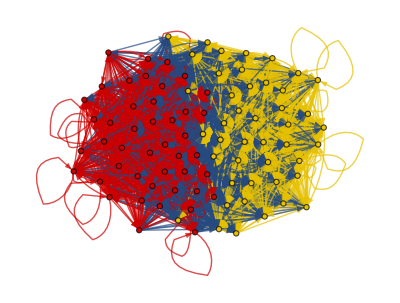

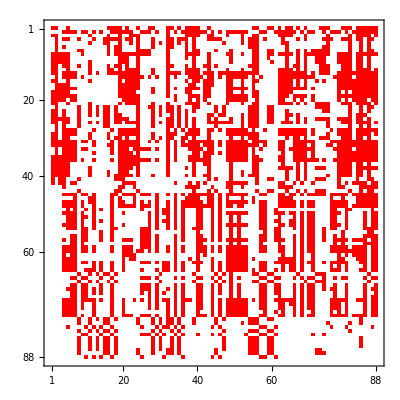

```mathematica
aa=FF2[[1]];
VR3= Reverse[VR2];
Thread[VR3-> newNames];

(*StringReplace[aa,Thread[VR3->newNames]]*)
reducedNet=Table[
Sort[ToExpression[StringTrim[StringSplit[StringReplace[FF2[[hh]],Thread[VR3->newNames]],{"&&","||"}]," "]]],{hh,1,Length[FF2],1}];
Length[reducedNet];

numNodes = Length[newNames];
newZerosCM = ConstantArray[0,{numNodes, numNodes}];
reducedCM=Table[
ReplacePart[newZerosCM[[jj]],Thread[reducedNet[[jj]]-> 1]],{jj,1,Length[newZerosCM],1}];
gg=Graph[connMatrix2EdgeList[reducedCM]["EdgeList"],EdgeStyle->Arrowheads[0.005]];
CommunityGraphPlot[gg,FindGraphCommunities[%]]

HighlightGraph[gg,Map[Subgraph[gg,#]&,FindGraphPartition[gg]]]
MatrixPlot[AdjacencyMatrix[gg],ColorRules->{0->White,1->Red}]
```

```mathematica
Partitioning APOE-32 Graph
According to mathematica documentation, FindGraphPartition finds a partition of vertices such that the number of edges having endpoints in different parts is minized
```

-Graphics-

{{101,103,33},{2,5,61},{11,19,74},{59,95,53},{8,20,66},{3,7,25},{6,83,91},{27,81,39},{99,37,41},{40,54,56},{104,98,52},{50,18,100},{24,32,42},{30,58,110},{12,88,28},{17,29,31},{92,96,94},{62,82,44},{55,45},{77,85},{4,21},{1,71},{87,43},{57,105},{109,93},{73,89},{49,51},{65,47},{97,35},{63,68},{75,107},{36,34},{106,46},{48,60},{10,80},{26,102},{15,22},{67,64},{86,84},{14,38},{16,72},{79,69},{76,78},{13,90},{23,108},{9,70},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{}}

80

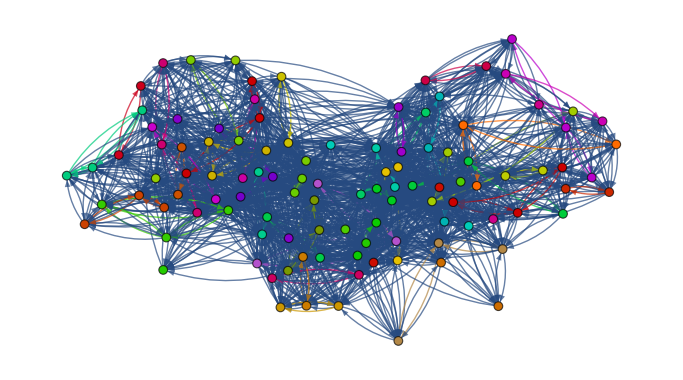

```mathematica
cm2=Import["/Users/macbookpro/Documents/03_REDUCTION_NETWORKS/APOE-3_2cmBinSOURCE.csv","CSV"];
dyn2=
[110]["Dynamic"];
connMatrix2EdgeList[cm2];
gg2=Graph[connMatrix2EdgeList[cm2]["EdgeList"],EdgeStyle->Arrowheads[0.03]];
CommunityGraphPlot[gg2,FindGraphCommunities[%]]


fortyPartitions=FindGraphPartition[gg2,80]
Length[fortyPartitions]
HighlightGraph[gg2,Map[Subgraph[gg2,#]&,FindGraphPartition[gg2,80]]]
```

```mathematica
One option is to look for the node with min of connections. Afted find it to take adjacent nodes to spread analysis towards all the network
```

```mathematica
(*1. Identify the node with min input nodes*)
numConn=Length[#]&/@(Flatten[Position[#,1]]&/@cm2);
nodeMinInputConnections=Flatten[Position[numConn,Min[numConn]]];
partition=nodeMinInputConnections;
sub1=Part[cm2,partition];

(*2. Get all input nodes*)
Print["Input nodes: "];
nodeInputs=DeleteDuplicates[Flatten[Sort[Position[#,1]&/@sub1]]];

(*3. Get al output nodes*)
Print["Output Nodes:"];
nodeOutputs=Flatten[Position[Flatten[cm2[[All,nodeMinInputConnections]]],1]]
HighlightGraph[gg2,{nodeInputs,Style[partition,Green]}]

(*4. Construct subgraph with (1),(2) and (3)*)
Print["inputs and ouputs nodes: "];
all=DeleteDuplicates[
[nodeInputs,partition, nodeOutputs]];


Print["Subgraph:"];
partGraph=Subgraph[gg2,all]
Print["New adjacency matrix;"];
allCM=Normal[AdjacencyMatrix[partGraph]];
Print["New Dynamic:"];
allDyn=createRandomDynamic[Length[allCM]]["Dynamic"];
HighlightGraph[partGraph,Style[partition,Red]]


runNetwork = runDynamic[allCM,allDyn,"inverse"];
myInputs=runNetwork["RepertoireInputs"];
myOutputs = runNetwork["RepertoireOutputs"];
myAttractors = runNetwork["Attractors"];
aba=analysisBasinsAttraction[myInputs,myOutputs];
aba["ChangeInNodes"]
aba["EffectInNodes"]
```

Input nodes:

Output Nodes:

{3,15,19,23,25,27,47}

-Graphics-

inputs and ouputs nodes:

Subgraph:

-Graphics-

New adjacency matrix;

New Dynamic:

-Graphics-

{{8},{7},{3},{2,3,4,5,6,7,8},{1,2,3,4,5,7,8},{1,2,3,4,5,6,7,8},{4,7},{2,7},{1,2,3,4,5,6,7,8},{2,4,5,7},{1,2,3,4,5,6,7,8}}

{{2,3,4,7},{3,8},{2,4,7,8},{1,2,3,4,7,8},{2,3,4,6,7,8},{1,2,3,4,5,6,7,8},{2,3,8},{3,4,8},{2,3,4,5,7,8},{2,3,4,8},{2,3,4,7,8}}

```mathematica
Automatic adjacecy matrix and Phi style connection matrix have different interpretation and visualization
```

```mathematica
MatrixPlot[AdjacencyMatrix[gg2],ColorRules->{0->White,1->Red}]
MatrixPlot[cm2,ColorRules->{0->White,1->Red}]
AdjacencyMatrix[gg2]//MatrixForm;
cm2//MatrixForm;
```

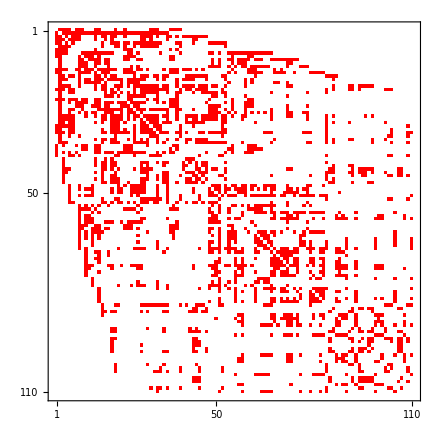

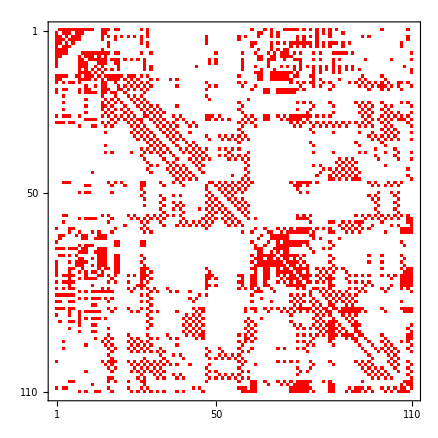

```mathematica
Applying bridges (batches) analysis to APOE-32 network
```

{{29,87,47,103,33,41,43,45},{3,6,81,63,21,23,25},{1,8,67,89,59,70},{7,10,15,85,68,84},{5,17,19,61,65,107},{4,27,74,57,37,55},{11,66,18,28,48,104},{12,76,30,110,96,108},{16,20,86,13,88,94},{99,39,49,51,53},{2,75,83,69,93},{73,77,79,97,105},{109,95,91,90,92},{50,58,38,106,46},{62,78,80,82,44},{32,36,60,40,42},{100,34,52,54,56},{22,24,26,102,98},{71,101,31,35},{9,72,64,14}}

20

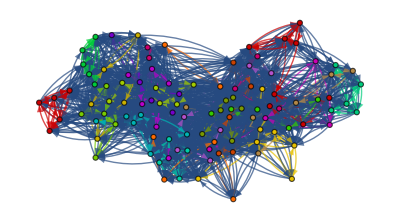

```mathematica
(* 1. partition network*)
cm2=Import["/Users/macbookpro/Documents/03_REDUCTION_NETWORKS/APOE-3_2cmBinSOURCE.csv","CSV"];
dyn2=createRandomDynamic[110]["Dynamic"];
connMatrix2EdgeList[cm2];
gg2=Graph[connMatrix2EdgeList[cm2]["EdgeList"],EdgeStyle->Arrowheads[0.03]];
subnetworks=FindGraphPartition[gg2,20] /.{}->Sequence[]
Length[subnetworks]

(* 2. showing graphs and parotion*)

HighlightGraph[gg2,Map[Subgraph[gg2,#]&,FindGraphPartition[gg2,20]]]
```

```mathematica
Patitions is above try do not assure to result connected partitions. Here I try clustering to partition network (yes, it works!!)
```

```mathematica
(*Table[HighlightGraph[gg2,Part[subnetworks,ee]],{ee,1,Length[subnetworks],1}]
Table[Graph[Subgraph[gg2,Part[subnetworks,rr]]],{rr,1, Length[subnetworks],1}]*)

(*2. Using grPartitoin that explote spectral clustering*)
clustering = Import["/Users/macbookpro/Documents/03_REDUCTION_NETWORKS/clusterionAPOE-3_2.csv","CSV"];
ass=Association[#]&/@Thread[ Flatten[clustering]->  Range[1,110]];
Print["Subnetworks2"];
subnetworks2=Values[Merge[ass, Identity]]

(*Table[HighlightGraph[gg2,Part[subnetworks2,ee]],{ee,1,Length[subnetworks2],1}]
Table[Graph[Subgraph[gg2,Part[subnetworks2,rr]]],{rr,1, Length[subnetworks2],1}]*)


(* 3. Getting schemata for all possible partitions and in consequence all valid
combinations purview-mechanism. In alpha terms: source-effect*)
calculateSchemata4SetSubnetworks[gg2,dyn2,subnetworks2];
```

Subnetworks2

{{1,2,4,7,9,14,63,64,67,68},{3,15,17,21,23,25,79,95},{5,6,81,83,89,91},{8,10,11,12,13,82,84},{16,20,22,26,28},{18,24,30,32,34,38,80,96,102},{19,27,65,69,70,71,72,73},{29,31,35,37,41,43,45,59,87,93},{33,97,99,101,103,105},{36,42,44,46,88,90},{39,47,49,51,53,55,57},{40,48,50,52,54,56,58},{60,92,94,109,110},{61,75,77,85,107},{62,66,74,76,78,86,108},{98,100,104,106}}

First Subgraph and its edge list

-Graphics-

{2->1,1->2,4->1,4->2,1->4,2->4,7->1,7->2,7->4,1->7,2->7,4->7,9->1,9->2,1->9,2->9,14->9,9->14,63->2,63->7,63->9,63->14,2->63,7->63,9->63,14->63,64->2,64->9,64->14,64->63,2->64,9->64,14->64,63->64,67->1,67->2,67->7,67->9,67->14,67->63,67->64,1->67,2->67,7->67,9->67,14->67,63->67,64->67,68->9,68->14,68->63,68->64,68->67,9->68,14->68,63->68,64->68,67->68}

Origin

{{1,2,4,7,9,14,63,64,67,68},{3,15,17,21,23,25,79,95},{5,6,81,83,89,91},{8,10,11,12,13,82,84},{16,20,22,26,28},{18,24,30,32,34,38,80,96,102},{19,27,65,69,70,71,72,73},{29,31,35,37,41,43,45,59,87,93},{33,97,99,101,103,105},{36,42,44,46,88,90},{39,47,49,51,53,55,57},{40,48,50,52,54,56,58},{60,92,94,109,110},{61,75,77,85,107},{62,66,74,76,78,86,108},{98,100,104,106}}

Ends:

{{1,2,4,7,9,14,63,64,67,68},{3,15,17,21,23,25,79,95},{5,6,81,83,89,91},{8,10,11,12,13,82,84},{16,20,22,26,28},{18,24,30,32,34,38,80,96,102},{19,27,65,69,70,71,72,73},{29,31,35,37,41,43,45,59,87,93},{33,97,99,101,103,105},{36,42,44,46,88,90},{39,47,49,51,53,55,57},{40,48,50,52,54,56,58},{60,92,94,109,110},{61,75,77,85,107},{62,66,74,76,78,86,108},{98,100,104,106}}

All outputs from first subnetwork

{2->1,4->1,7->1,9->1,67->1,1->2,4->2,7->2,9->2,63->2,64->2,67->2,1->3,2->3,4->3,7->3,63->3,67->3,1->4,2->4,7->4,1->5,2->5,4->5,67->5,1->6,4->6,67->6,1->7,2->7,4->7,63->7,67->7,1->8,2->8,4->8,9->8,14->8,68->8,1->9,2->9,14->9,63->9,64->9,67->9,68->9,1->10,9->10,14->10,63->10,64->10,67->10,68->10,1->11,9->11,14->11,1->12,9->12,14->13,64->13,68->13,9->14,63->14,64->14,67->14,68->14,1->15,2->15,4->15,7->15,14->15,63->15,64->15,67->15,68->15,1->16,2->16,9->16,63->16,64->16,67->16,68->16,1->17,1->19,4->19,1->20,1->27,4->27,1->29,2->29,4->47,4->57,1->61,14->62,67->62,2->63,7->63,9->63,14->63,64->63,67->63,68->63,2->64,9->64,14->64,63->64,67->64,68->64,1->65,1->67,2->67,7->67,9->67,14->67,63->67,64->67,68->67,9->68,14->68,63->68,64->68,67->68,2->69,7->69,14->69,63->69,64->69,67->69,68->69,9->70,14->70,63->70,64->70,67->70,1->71,7->71,9->71,14->71,63->71,64->71,67->71,68->71,1->72,7->72,9->72,14->72,63->72,64->72,67->72,68->72,1->73,9->73,14->73,1->74,1->75,4->75,14->75,1->77,4->77,1->79,63->79,67->79,14->80,63->80,64->80,68->80,1->81,2->81,4->81,14->82,64->82,1->83,2->83,67->83,1->85,2->85,67->85,14->86,1->87,14->88,64->88,2->89,1->101,1->109,4->109,14->110}

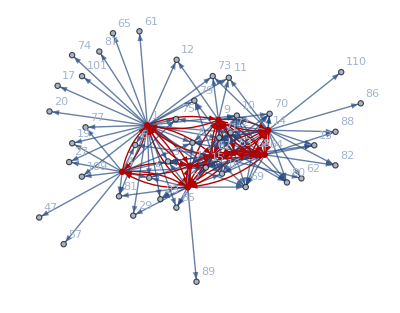

```mathematica
(*For finding bridges, edgeList of complete graph is used as set of rules*)
connRules = EdgeList[gg2];

Print["First Subgraph and its edge list"];
sg2=Subgraph[gg2,subnetworks2[[1]]]
el2=EdgeList[Subgraph[gg2,subnetworks2[[1]]]]

(*All origins and ends*)
Print["Origin"];
origin=Sort[#]&/@(DeleteDuplicates[#]&/@(#[[1]]&/@EdgeList[Subgraph[gg2,#]]&/@subnetworks2))
Print["Ends:"];
end=Sort[#]&/@(DeleteDuplicates[#]&/@(#[[2]]&/@EdgeList[Subgraph[gg2,#]]&/@subnetworks2))

(*Give me all elements of edge list of the complete graph wich first element is in
the first list of origins, these are all connections that get out from first subnetwork*)

Print["All outputs from first subnetwork"]
allOutputsFromFirstSubNet =Table[If[Length[Position[origin[[1]],First[connRules[[ss]]]]]>0,connRules[[ss]],Null],{ss,1,Length[connRules],1}]/.Null->Sequence[]
g1=Graph[%,VertexLabels->"Name"];
HighlightGraph[g1,sg2]
```

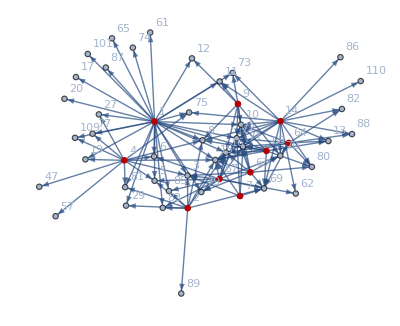

```mathematica
extg=Graph[Complement[allOutputsFromFirstSubNet,el2],VertexLabels->"Name"];
HighlightGraph[extg,sg2]
```

```mathematica
Finding bridges
```

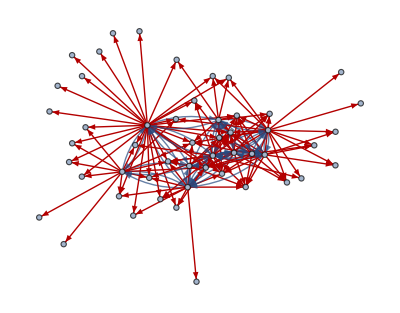

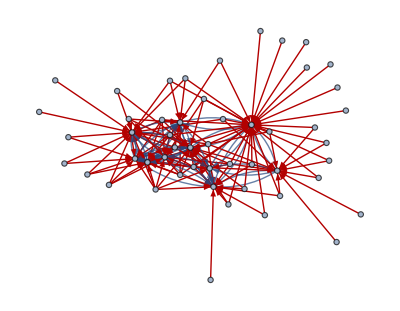

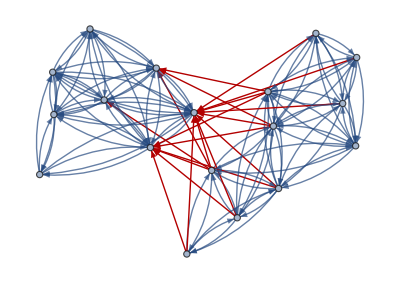

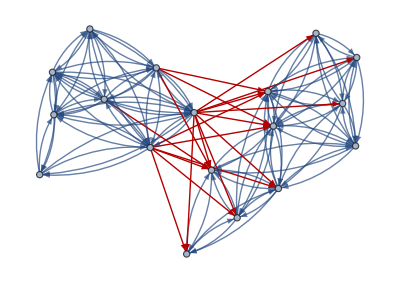

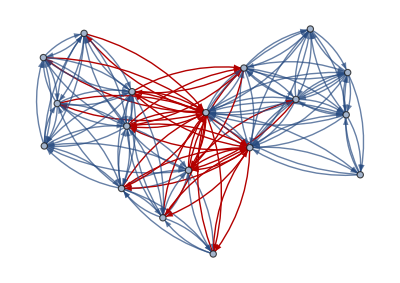

```mathematica
sn1=EdgeList[Subgraph[gg2,subnetworks2[[1]]]];
sn2=EdgeList[Subgraph[gg2,subnetworks2[[2]]]];
sn12 = Join[sn1,sn2];

fb=findBridges[connRules,sn1,sn2];
aoGraph=Graph[fb["AllOutputs"]];
aiGraph=Graph[fb["AllInputs"]];
HighlightGraph[aoGraph,fb["OutBridges"]]
HighlightGraph[aiGraph,fb["InBridges"]]
HighlightGraph[Graph[Union[sn12,fb["Bridges2G2"]]],fb["Bridges2G2"]]

HighlightGraph[Graph[Union[sn12,fb["Bridges2G1"]]],fb["Bridges2G1"]]

HighlightGraph[Graph[Union[sn12,fb["Bridges"]]],fb["Bridges"]]
```

```mathematica
fb["Bridges"]
```

{1->3,2->3,4->3,7->3,63->3,67->3,1->15,2->15,4->15,7->15,14->15,63->15,64->15,67->15,68->15,1->17,1->79,63->79,67->79,3->1,3->2,3->4,3->7,3->63,3->67,15->1,15->2,15->4,15->7,15->14,15->63,15->64,15->67,15->68,17->1,79->1,79->63,79->67}

```mathematica
oneSourceScheA={2,4};
oneEndSchA={1,2};
 sourceSetScheA= {{2,4},{1,2,3,4},{2,3,4}};
endSetScheA={{1,2},{1,2,3,4},{1,2,4}};
sourceSetSchB = {{5,6,7,9},{5,7,9},{5,6,9},{5,9},{5,6,7},{5,7}};
endSetSchB = {{5,6,7,9},{5,6,9},{5,7,9},{5,9},{7,9},{9}};
```

```mathematica
combineSchemataSets[sourceSetScheA,sourceSetSchB]
```

{{{2,4,5,6,7,9},{2,4,5,7,9},{2,4,5,6,9},{2,4,5,9},{2,4,5,6,7},{2,4,5,7}},{{1,2,3,4,5,6,7,9},{1,2,3,4,5,7,9},{1,2,3,4,5,6,9},{1,2,3,4,5,9},{1,2,3,4,5,6,7},{1,2,3,4,5,7}},{{2,3,4,5,6,7,9},{2,3,4,5,7,9},{2,3,4,5,6,9},{2,3,4,5,9},{2,3,4,5,6,7},{2,3,4,5,7}}}

```mathematica
sourceSetScheA= {{1},{2},{1,2,3},{2,4},{1,2,3,4},{2,3,4}};
endSetScheA={{4},{1},{1,4},{1,2},{1,2,3,4},{1,2,4}};
sourceSetSchB = {{5,6,7,9},{5,7,9},{5,6,9},{5,9},{9},{5,6,7},{5,7}};
endSetSchB = {{5,6,7,9},{5,6,9},{5,7,9},{5,9},{5},{7,9},{9}};
ruleTest=DirectedEdge[4, 5];
```

```mathematica
selectSetByRule[sourceSetScheA,sourceSetSchB,ruleTest]
```

<|OriginsA→{{2,4},{1,2,3,4},{2,3,4}},OriginsB→{{5,6,7,9},{5,7,9},{5,6,9},{5,9},{5,6,7},{5,7}},OriginIndexesA→{4,5,6},OriginIndexesB→{1,2,3,4,6,7}|>

```mathematica
originSetScheA= {{1},{2},{1,2,3},{2,4},{1,2,3,4},{2,3,4}};
effectSetScheA={{4},{1},{1,4},{1,2},{1,2,3,4},{1,2,4}};
originSetSchB = {{5,6,7,9},{5,7,9},{5,6,9},{5,9},{9},{5,6,7},{5,7}};
effectSetSchB = {{5,6,7,9},{5,6,9},{5,7,9},{5,9},{5},{7,9},{9}};
ruleTest=DirectedEdge[4, 5];
```

```mathematica
joinSchematByRule[originSetScheA,effectSetScheA,originSetSchB,effectSetSchB,ruleTest]
```

<|JoinedOrigins→{{{2,4,5,6,7,9},{2,4,5,7,9},{2,4,5,6,9},{2,4,5,9},{2,4,5,6,7},{2,4,5,7}},{{1,2,3,4,5,6,7,9},{1,2,3,4,5,7,9},{1,2,3,4,5,6,9},{1,2,3,4,5,9},{1,2,3,4,5,6,7},{1,2,3,4,5,7}},{{2,3,4,5,6,7,9},{2,3,4,5,7,9},{2,3,4,5,6,9},{2,3,4,5,9},{2,3,4,5,6,7},{2,3,4,5,7}}},JoinedEffects→{{{1,2,5,6,7,9},{1,2,5,6,9},{1,2,5,7,9},{1,2,5,9},{1,2,7,9},{1,2,9}},{{1,2,3,4,5,6,7,9},{1,2,3,4,5,6,9},{1,2,3,4,5,7,9},{1,2,3,4,5,9},{1,2,3,4,7,9},{1,2,3,4,9}},{{1,2,4,5,6,7,9},{1,2,4,5,6,9},{1,2,4,5,7,9},{1,2,4,5,9},{1,2,4,7,9},{1,2,4,9}}}|>

```mathematica
originSetScheA= {{1},{2},{1,2,3},{2,4},{1,2,3,4},{2,3,4}};
effectSetScheA={{4},{1},{1,4},{1,2},{1,2,3,4},{1,2,4}};
originSetSchB = {{5,6,7,9},{5,7,9},{5,6,9},{5,9},{9},{5,6,7},{5,7}};
effectSetSchB = {{5,6,7,9},{5,6,9},{5,7,9},{5,9},{5},{7,9},{9}};
ruleSetTestAB={DirectedEdge[4, 5],DirectedEdge[4, 6],DirectedEdge[4, 7]};
ruleSetTestBA={DirectedEdge[ 6,4],DirectedEdge[7,4]};
```

```mathematica
go=joinSchematBySetRules[originSetScheA,effectSetScheA, originSetSchB, effectSetSchB, ruleSetTestAB]
back=joinSchematBySetRules[ originSetSchB, effectSetSchB,originSetScheA,effectSetScheA, ruleSetTestBA]
```

{{{{2,4,5,6,7,9},{2,4,5,7,9},{2,4,5,6,9},{2,4,5,9},{2,4,5,6,7},{2,4,5,7}},{{1,2,3,4,5,6,7,9},{1,2,3,4,5,7,9},{1,2,3,4,5,6,9},{1,2,3,4,5,9},{1,2,3,4,5,6,7},{1,2,3,4,5,7}},{{2,3,4,5,6,7,9},{2,3,4,5,7,9},{2,3,4,5,6,9},{2,3,4,5,9},{2,3,4,5,6,7},{2,3,4,5,7}}},{{{2,4,5,6,7,9},{2,4,5,6,9},{2,4,5,6,7}},{{1,2,3,4,5,6,7,9},{1,2,3,4,5,6,9},{1,2,3,4,5,6,7}},{{2,3,4,5,6,7,9},{2,3,4,5,6,9},{2,3,4,5,6,7}}},{{{2,4,5,6,7,9},{2,4,5,7,9},{2,4,5,6,7},{2,4,5,7}},{{1,2,3,4,5,6,7,9},{1,2,3,4,5,7,9},{1,2,3,4,5,6,7},{1,2,3,4,5,7}},{{2,3,4,5,6,7,9},{2,3,4,5,7,9},{2,3,4,5,6,7},{2,3,4,5,7}}}}

{{{{1,2,5,6,7,9},{1,2,5,6,9},{1,2,5,7,9},{1,2,5,9},{1,2,7,9},{1,2,9}},{{1,2,3,4,5,6,7,9},{1,2,3,4,5,6,9},{1,2,3,4,5,7,9},{1,2,3,4,5,9},{1,2,3,4,7,9},{1,2,3,4,9}},{{1,2,4,5,6,7,9},{1,2,4,5,6,9},{1,2,4,5,7,9},{1,2,4,5,9},{1,2,4,7,9},{1,2,4,9}}},{{{1,2,5,6,7,9},{1,2,5,7,9},{1,2,7,9}},{{1,2,3,4,5,6,7,9},{1,2,3,4,5,7,9},{1,2,3,4,7,9}},{{1,2,4,5,6,7,9},{1,2,4,5,7,9},{1,2,4,7,9}}},{{{1,2,5,6,7,9},{1,2,5,6,9},{1,2,7,9},{1,2,9}},{{1,2,3,4,5,6,7,9},{1,2,3,4,5,6,9},{1,2,3,4,7,9},{1,2,3,4,9}},{{1,2,4,5,6,7,9},{1,2,4,5,6,9},{1,2,4,7,9},{1,2,4,9}}}}

<|NewOrigins→{{2,4,5,6,7,9},{2,4,5,7,9},{2,4,5,6,9},{2,4,5,9},{2,4,5,6,7},{2,4,5,7},{1,2,3,4,5,6,7,9},{1,2,3,4,5,7,9},{1,2,3,4,5,6,9},{1,2,3,4,5,9},{1,2,3,4,5,6,7},{1,2,3,4,5,7},{2,3,4,5,6,7,9},{2,3,4,5,7,9},{2,3,4,5,6,9},{2,3,4,5,9},{2,3,4,5,6,7},{2,3,4,5,7},{2,4,5,6,7,9},{2,4,5,6,9},{2,4,5,6,7},{1,2,3,4,5,6,7,9},{1,2,3,4,5,6,9},{1,2,3,4,5,6,7},{2,3,4,5,6,7,9},{2,3,4,5,6,9},{2,3,4,5,6,7},{2,4,5,6,7,9},{2,4,5,7,9},{2,4,5,6,7},{2,4,5,7},{1,2,3,4,5,6,7,9},{1,2,3,4,5,7,9},{1,2,3,4,5,6,7},{1,2,3,4,5,7},{2,3,4,5,6,7,9},{2,3,4,5,7,9},{2,3,4,5,6,7},{2,3,4,5,7}},NewEffects→{{1,2,5,6,7,9},{1,2,5,6,9},{1,2,5,7,9},{1,2,5,9},{1,2,7,9},{1,2,9},{1,2,3,4,5,6,7,9},{1,2,3,4,5,6,9},{1,2,3,4,5,7,9},{1,2,3,4,5,9},{1,2,3,4,7,9},{1,2,3,4,9},{1,2,4,5,6,7,9},{1,2,4,5,6,9},{1,2,4,5,7,9},{1,2,4,5,9},{1,2,4,7,9},{1,2,4,9},{1,2,5,6,7,9},{1,2,5,7,9},{1,2,7,9},{1,2,3,4,5,6,7,9},{1,2,3,4,5,7,9},{1,2,3,4,7,9},{1,2,4,5,6,7,9},{1,2,4,5,7,9},{1,2,4,7,9},{1,2,5,6,7,9},{1,2,5,6,9},{1,2,7,9},{1,2,9},{1,2,3,4,5,6,7,9},{1,2,3,4,5,6,9},{1,2,3,4,7,9},{1,2,3,4,9},{1,2,4,5,6,7,9},{1,2,4,5,6,9},{1,2,4,7,9},{1,2,4,9}}|>

{{{{2,4,5,6,7,9},{1,2,3,4,5,6,7,9},{2,3,4,5,6,7,9}},{{2,4,5,6,9},{1,2,3,4,5,6,9},{2,3,4,5,6,9}},{{2,4,5,6,7},{1,2,3,4,5,6,7},{2,3,4,5,6,7}}},{{{2,4,5,6,7,9},{1,2,3,4,5,6,7,9},{2,3,4,5,6,7,9}},{{2,4,5,7,9},{1,2,3,4,5,7,9},{2,3,4,5,7,9}},{{2,4,5,6,7},{1,2,3,4,5,6,7},{2,3,4,5,6,7}},{{2,4,5,7},{1,2,3,4,5,7},{2,3,4,5,7}}}}

{{{{1,2,5,6,7,9},{1,2,3,4,5,6,7,9},{1,2,4,5,6,7,9}},{{1,2,5,7,9},{1,2,3,4,5,7,9},{1,2,4,5,7,9}},{{1,2,7,9},{1,2,3,4,7,9},{1,2,4,7,9}}},{{{1,2,5,6,7,9},{1,2,3,4,5,6,7,9},{1,2,4,5,6,7,9}},{{1,2,5,6,9},{1,2,3,4,5,6,9},{1,2,4,5,6,9}},{{1,2,7,9},{1,2,3,4,7,9},{1,2,4,7,9}},{{1,2,9},{1,2,3,4,9},{1,2,4,9}}}}

<|NewOrigins→{{2,4,5,6,7,9},{1,2,3,4,5,6,7,9},{2,3,4,5,6,7,9},{2,4,5,6,9},{1,2,3,4,5,6,9},{2,3,4,5,6,9},{2,4,5,6,7},{1,2,3,4,5,6,7},{2,3,4,5,6,7},{2,4,5,6,7,9},{1,2,3,4,5,6,7,9},{2,3,4,5,6,7,9},{2,4,5,7,9},{1,2,3,4,5,7,9},{2,3,4,5,7,9},{2,4,5,6,7},{1,2,3,4,5,6,7},{2,3,4,5,6,7},{2,4,5,7},{1,2,3,4,5,7},{2,3,4,5,7}},NewEffects→{{1,2,5,6,7,9},{1,2,3,4,5,6,7,9},{1,2,4,5,6,7,9},{1,2,5,7,9},{1,2,3,4,5,7,9},{1,2,4,5,7,9},{1,2,7,9},{1,2,3,4,7,9},{1,2,4,7,9},{1,2,5,6,7,9},{1,2,3,4,5,6,7,9},{1,2,4,5,6,7,9},{1,2,5,6,9},{1,2,3,4,5,6,9},{1,2,4,5,6,9},{1,2,7,9},{1,2,3,4,7,9},{1,2,4,7,9},{1,2,9},{1,2,3,4,9},{1,2,4,9}}|>

```mathematica
setTestRules = {DirectedEdge[4, 5],DirectedEdge[4, 6],DirectedEdge[5,4],DirectedEdge[4, 7]};
```

```mathematica
detectDeleteInverseRules[setTestRules]
```

<|CleanSetRules→{4->5,4->6,4->7}|>

```mathematica
This is a full example 1
```

{0,0,0,0,0,0,0,0,0,0,0,0}

{{1,2,3,4},{5,6,7,9},{8,10,11,12}}

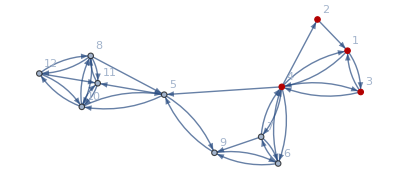

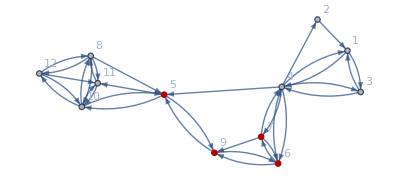

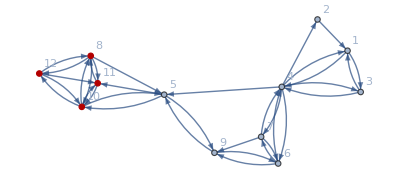

```mathematica
edgeListExample1={{1->3 },{1->4 },{2->1 },{3->1 },{3->4 },{4->1 },{4->2 },{4->3 },{4->5 },{4->6 },{4->7 },{6->4 },{7->4 },{8->10 },{8-> 5},{5->10 },{5->11 },{10->5 },{10->11},{10-> 8},{11->10 },{9->5 },{10->12 },{8->11 },{5->9 },{6->7 },{6->9 },{7->6 },{7->9 },{9->6 },{8->12 },{11->8 },{12->8 },{12->10 },{12-> 11}};
graphExample1=Graph[Flatten[edgeListExample1],VertexLabels->"Name"];
cmExample1=Normal[ Transpose[AdjacencyMatrix[Graph[Flatten[edgeListExample1]]]]];
dynExample1={"OR","OR","AND","OR","AND","OR","OR","AND","AND","OR","OR","AND"};
csExample1= calculateOneOutptuOfNetwork[{0,0,0,0,0,0,0,0,0,0,0,0},cmExample1,dynExample1]["Output"]

example1={{1->3 ,1->4 ,2->1 ,3->1 ,3->4 ,4->1 ,4->2 ,4->3 },{9->5 ,9->6 ,5->9 ,6->7 ,6->9 ,7->6 ,7->9 },{8->10 ,8->11,8->12,10->11,10-> 8,10->12,11->8 ,11-> 12, 11->10 ,12->8 ,12->10 ,12-> 11}};
subnetworksExample1=Table[Sort[VertexList[Graph[example1[[gg]]]]],{gg,1,Length[example1],1}]

HighlightGraph[graphExample1,subnetworksExample1[[1]]]
HighlightGraph[graphExample1,subnetworksExample1[[2]]]
HighlightGraph[graphExample1,subnetworksExample1[[3]]]
```

```mathematica
calculateSchemata4SetSubnetworks[graphExample1,dynExample1,csExample1,subnetworksExample1]
```

<|Changes→{{{2},{1},{2,4},{2,3,4},{1,2,3,4},{1,2,3}},{{5,6,7},{5,6,7,9},{5,6,7},{7},{6},{7,9},{6,7,9}},{{11},{10},{10,11,12},{8,10,11,12},{8,10,11,12},{8,10,11,12}}},Effects→{{{1},{4},{1,2},{1,2,4},{1,2,3,4},{1,4}},{{6,7,9},{5,6,7,9},{6,7},{6},{7},{5,6},{5,6,7}},{{10},{11},{8,10,11},{8,10,11,12},{10,11,12},{10,11}}}|>

```mathematica
subnetworkNames=Range[1,Length[subnetworksExample1]];
allPossibleTuples=Subsets[subnetworkNames,2]
possibleCouples=Table[If[Length[Part[allPossibleTuples,ii]]>1,Part[allPossibleTuples,ii]],{ii,1,Length[allPossibleTuples],1}]/.Null->Sequence[]
allFirstSquemata=calculateSchemata4SetSubnetworks[graphExample1,dynExample1,csExample1,subnetworksExample1];
allOrigins=allFirstSquemata["Changes"]
allEffects = allFirstSquemata["Effects"]
```

{{},{1},{2},{3},{1,2},{1,3},{2,3}}

{{1,2},{1,3},{2,3}}

{{{2},{1},{2,4},{2,3,4},{1,2,3,4},{1,2,3}},{{5,6,7},{5,6,7,9},{5,6,7},{7},{6},{7,9},{6,7,9}},{{11},{10},{10,11,12},{8,10,11,12},{8,10,11,12},{8,10,11,12}}}

{{{1},{4},{1,2},{1,2,4},{1,2,3,4},{1,4}},{{6,7,9},{5,6,7,9},{6,7},{6},{7},{5,6},{5,6,7}},{{10},{11},{8,10,11},{8,10,11,12},{10,11,12},{10,11}}}

```mathematica
validCouples=List[];
allBridges = List[];
For[hh=1,hh≤Length[possibleCouples],hh++,
aCouple=Part[possibleCouples,hh];

vtxSubNet1=Part[subnetworksExample1,aCouple[[1]]];
vtxSubNet2=Part[subnetworksExample1,aCouple[[2]]];
edgeListSubNet1=EdgeList[Subgraph[graphExample1,vtxSubNet1]];
edgeListSubNet2=EdgeList[Subgraph[graphExample1,vtxSubNet2]];
bridges=findBridges[Flatten[edgeListExample1],edgeListSubNet1,edgeListSubNet2]["Bridges"];
bridges=detectDeleteInverseRules[bridges]["CleanSetRules"];

(* begin --------------------*)
(*Print[aCouple];
Print["VertexList1: "<> ToString[vtxSubNet1]];
Print["VertexList2: "<> ToString[vtxSubNet2]];
Print["EdgeList1: "<> ToString[edgeListSubNet1]];
Print["EdgeList2: "<> ToString[edgeListSubNet2]];
Print["Bridges: "<> ToString[bridges]];*)
(* end -----------------------*)


If[Length[bridges]>0,AppendTo[validCouples,aCouple];AppendTo[allBridges,Association[FromDigits[aCouple]-> bridges]],Null];
];
validCouples
allBridges=Merge[allBridges,Identity]

For[xx=1,xx≤ Length[validCouples],xx++,
aCouple = Part[validCouples,xx];
setOriginSchemataA = allOrigins[[aCouple[[1]]]];
setEffectSquemataA = allEffects[[aCouple[[1]]]];

setOriginSchemataB = allOrigins[[aCouple[[2]]]];
setEffectSquemataB = allEffects[[aCouple[[2]]]];

mixingRules =Flatten[ allBridges[FromDigits[aCouple]]];

(* begin -------------------*)
Print["--------------------------------------"];
Print["Origin Schemata A"<> ToString[setOriginSchemataA]];
Print["Effect Schemata A"<> ToString[setEffectSquemataA]];
Print["Origin Schemata B"<> ToString[setOriginSchemataB]];
Print["Effect Schemata B"<> ToString[setEffectSquemataB]];
Print["Mixing rules: " <> ToString[mixingRules]];
 
(* end ----------------------*)
joinedSche=joinSchematBySetRules[setOriginSchemataA,setEffectSquemataA,setOriginSchemataB,setEffectSquemataB,Flatten[allBridges[FromDigits[aCouple]]]];

no=joinedSche["NewOrigins"];
ne=joinedSche["NewEffects"];
Print["All new origins:"<> ToString[Length[no]]];
Print[no];
Print["All new Effects: "<> ToString[Length[ne]]];
Print[ne];


noneAss=DeleteDuplicates[Table[Association[<|no[[ww]]->ne[[ww]]|>],{ww,1,Length[joinedSche["NewOrigins"]],1}]];
Print["Associations Origins -> Effects:"<> ToString[Length[noneAss]]];
Print[noneAss];


noneMerged=Merge[noneAss,Identity];
Print["Association Merged: "<> ToString[Length[noneMerged]]];
Print[noneMerged];

];
```

{}

<||>

```mathematica
newVertex = Keys[allBridges]
couples=Table[IntegerDigits[newVertex[[gg]]],{gg,1,Length[newVertex],1}]

unitedVertex=List[];
For[pp=1, pp≤ Length[couples],pp++,
sg1=Sort[VertexList[Subgraph[graphExample1,example1[[couples[[pp]][[1]]]]]]];
sg2=Sort[VertexList[Subgraph[graphExample1,example1[[couples[[pp]][[2]]]]]]];
nv=Union[sg1,sg2];
AppendTo[unitedVertex,nv];

];
unitedVertex
inter=Intersection[unitedVertex[[1]],unitedVertex[[2]]]
Complement[unitedVertex[[2]],inter]
```

Keys::invrl: The argument Keys[allBridges] is not a valid Association or a list of rules.

Keys[allBridges]

{IntegerDigits[allBridges]}

Part::pkspec1: The expression allBridges cannot be used as a part specification.

VertexList::graph: A graph object is expected at position 1 in VertexList[Subgraph[graphExample1, example1 ⟦ allBridges ⟧]].

Part::pkspec1: The expression allBridges cannot be used as a part specification.

VertexList::graph: A graph object is expected at position 1 in VertexList[Subgraph[graphExample1, example1 ⟦ allBridges ⟧]].

Part::partw: Part 2 of IntegerDigits[allBridges] does not exist.

Part::pkspec1: The expression IntegerDigits[allBridges] ⟦ 2 ⟧ cannot be used as a part specification.

General::stop: Further output of Part :: pkspec1 will be suppressed during this calculation.

VertexList::graph: A graph object is expected at position 1 in VertexList[Subgraph[graphExample1, example1 ⟦ IntegerDigits[allBridges] ⟦ 2 ⟧ ⟧]].

General::stop: Further output of VertexList :: graph will be suppressed during this calculation.

{VertexList[Subgraph[graphExample1,example1⟦allBridges⟧],Subgraph[graphExample1,example1⟦IntegerDigits[allBridges]⟦2⟧⟧]]}

Part::partw: Part 2 of {VertexList[Subgraph[graphExample1, example1 ⟦ allBridges ⟧], Subgraph[graphExample1, example1 ⟦ IntegerDigits[allBridges] ⟦ 2 ⟧ ⟧]]} does not exist.

Intersection::heads: Heads Part and VertexList at positions 2 and 1 are expected to be the same.

VertexList[Subgraph[graphExample1,example1⟦allBridges⟧],Subgraph[graphExample1,example1⟦IntegerDigits[allBridges]⟦2⟧⟧]]∩{VertexList[Subgraph[graphExample1,example1⟦allBridges⟧],Subgraph[graphExample1,example1⟦IntegerDigits[allBridges]⟦2⟧⟧]]}⟦2⟧

Part::partw: Part 2 of {VertexList[Subgraph[graphExample1, example1 ⟦ allBridges ⟧], Subgraph[graphExample1, example1 ⟦ IntegerDigits[allBridges] ⟦ 2 ⟧ ⟧]]} does not exist.

Complement::heads: Heads Intersection and Part at positions 2 and 1 are expected to be the same.

Complement[{VertexList[Subgraph[graphExample1,example1⟦allBridges⟧],Subgraph[graphExample1,example1⟦IntegerDigits[allBridges]⟦2⟧⟧]]}⟦2⟧,VertexList[Subgraph[graphExample1,example1⟦allBridges⟧],Subgraph[graphExample1,example1⟦IntegerDigits[allBridges]⟦2⟧⟧]]∩{VertexList[Subgraph[graphExample1,example1⟦allBridges⟧],Subgraph[graphExample1,example1⟦IntegerDigits[allBridges]⟦2⟧⟧]]}⟦2⟧]

```mathematica
SECOND TRY
```

```mathematica
(*
****************************************************************Defining system***************************************************************)edgeListFullExample1={1->3,1->4,2->1,3->1,3->4,4->1,4->2,4->3,4->5,4->6,4->7,6->4,7->4,8->10,8->5,5->10,5->11,10->5,10->11,10->8,11->10,9->5,10->12,8->11,5->9,6->7,6->9,7->6,7->9,9->6,8->12,11->8,12->8,12->10,12->11,11->12};
graphExample1=Graph[edgeListFullExample1,VertexLabels->"Name"];
cmExample1=Normal[Transpose[AdjacencyMatrix[Graph[edgeListFullExample1]]]];
dynExample1={"OR","OR","AND","OR","AND","OR","OR","AND","AND","OR","OR","AND"};
csExample1=calculateOneOutptuOfNetwork[{0,0,0,0,0,0,0,0,0,0,0,0},cmExample1,dynExample1]["Output"];

subnetworksExample1={{1->3,1->4,2->1,3->1,3->4,4->1,4->2,4->3},{9->5,9->6,5->9,6->7,6->9,7->6,7->9},{8->10,8->11,8->12,10->11,10->8,10->12,11->8,11->12,11->10,12->8,12->10,12->11}};

(*vertex list of subnetworks*)

vlsubnetworksExample1=Table[Sort[VertexList[Graph[subnetworksExample1[[gg]]]]],{gg,1,Length[subnetworksExample1],1}];

(*
****************************************************************Schemata definitions of each subnetwork and saving to disk***************************************************************)

firstSch=calculateSchemata4SetSubnetworks[graphExample1,dynExample1,csExample1,vlsubnetworksExample1];


(*All schemata in memory*)
allOriginSch=firstSch["Origins"];
allEffectSch=firstSch["Effects"];

Print[" FIRST ALL SCHEMATA ----------"];
Print[allOriginSch];
Print[allEffectSch];

(*All schemata in disk*)
(*savePath="/Users/macbookpro/Documents/ALPHA_TEST_12NODES/";
Do[Export[savePath<>"OriginSchemata"<>ToString[ff]<>".csv",allOriginSch[[ff]],"CSV"],{ff,1,Length[allOriginSch],1}];
Do[Export[savePath<>"EffectSchemata"<>ToString[ff]<>".csv",allEffectSch[[ff]],"CSV"],{ff,1,Length[allEffectSch],1}];*)

(*
****************************************************************Giving names to each subnetwork.Pivot network is the first in the list and taked out from list of names***************************************************************)

subsetNames=Range[1,Length[subnetworksExample1]];
allOriginSch = Merge[Table[Association[<|Part[subsetNames,yy]-> Part[allOriginSch,yy]|>],{yy,1,Length[allOriginSch],1}],Identity];
allEffectSch =Merge[ Table[Association[<|Part[subsetNames,yy]-> Part[allEffectSch,yy]|>],{yy,1,Length[allOriginSch],1}],Identity];

Print["Schemata sets with association to a name --------------"];
Print[allOriginSch];
Print[allEffectSch];
Print["-------------------------------------------------------"];
Print["-------------------------------------------------------"];

pivote=subsetNames[[1]];
subsetNames=DeleteCases[subsetNames,pivote];

Print["** PIVOTE ** : " <> ToString[pivote]];

(*
*****************************************************************Main idea is to find bridges between pivot and eny other subnetwork.When bridges are found,pivot and the other subnetwork are joined to construct the new pivot.
*****************************************************************)

While[Length[subsetNames]>0,
added=List[];

For[rr=1,rr≤Length[subsetNames],rr++,(*compara pivote subnetwork to each other subnetwork find bridges and remove inverses.bridges={4->2,2->4} then bridges={4,2}*)
oneSubnetwork=subnetworksExample1[[subsetNames[[rr]]]];
subnetworkPivote=Flatten[subnetworksExample1[[pivote]]];
bridges=findBridges[edgeListFullExample1,subnetworkPivote,oneSubnetwork]["Bridges"];
bridges=detectDeleteInverseRules[bridges]["CleanSetRules"];
Print["Subnetwork pivote: "<>ToString[subnetworkPivote]];
Print["choosed subnetwork: "<>ToString[oneSubnetwork]];
Print["Found bridges: "<>ToString[bridges]];


If[Length[bridges]>0,(*pivoteOriginSch=Import[savePath<>"OriginSchemata"<>ToString[pivote]<>".csv","CSV"];
pivoteEffectSch=Import[savePath<>"EffectSchemata"<>ToString[pivote]<>".csv","CSV"];
oneSubnetOriginSche=Import[savePath<>"OriginSchemata"<>ToString[subsetNames[[rr]]]<>".csv","CSV"];
oneSubnetEffectSche=Import[savePath<>"EffectSchemata"<>ToString[subsetNames[[rr]]]<>".csv","CSV"];*)



pivoteOriginSch=Level[allOriginSch[Key[pivote]],{-2}];
pivoteEffectSch=Level[allEffectSch[Key[pivote]],{-2}];

If[Length[pivote]>1,
For[vv=1,vv≤Length[pivote],vv++,
Print[allOriginSch[Key[Part[pivote,vv]]]];
pivoteOriginSch=Level[Join[pivoteOriginSch,allOriginSch[Key[Part[pivote,vv]]]],{-2}];
pivoteEffectSch=Level[Join[pivoteEffectSch,allEffectSch[Key[Part[pivote,vv]]]],{-2}];
];
,];

(*Print["----------- First extraction ---------------"];
Print[pivoteOriginSch];
Print[pivoteEffectSch];
Print["----------- First extraction ---------------"];*)



oneSubnetOriginSche=Level[allOriginSch[[subsetNames[[rr]]]],{-2}];
oneSubnetEffectSche=Level[allEffectSch[[subsetNames[[rr]]]],{-2}];
Print["pivote origin schemata: "<>ToString[pivoteOriginSch]];
Print["pivote effect schemata: "<>ToString[pivoteEffectSch]];
Print["Subnetwork origin schemata: "<>ToString[oneSubnetOriginSche]];
Print["Subnetwork effect schemata: "<>ToString[oneSubnetEffectSche]];


joinedSche=joinSchematBySetRules[pivoteOriginSch,pivoteEffectSch,oneSubnetOriginSche,oneSubnetEffectSche,bridges]/.{}->Sequence[];
originJoinedSche=joinedSche["NewOrigins"]/.{}->Sequence[];
effectJoinedSche=joinedSche["NewEffects"]/.{}->Sequence[];


Print["--------- JOINED --------"];
Print[Length[originJoinedSche]];
Print[originJoinedSche];
Print[effectJoinedSche];
(*Print["noneass: "<>ToString[Length[noneAss]]];
Print[noneAss];*)

noneAss=DeleteDuplicates[Table[Association[<|originJoinedSche[[ww]]->effectJoinedSche[[ww]]|>],{ww,1,Length[originJoinedSche],1}]]/.{}->Sequence[];
originJoinedSche=Level[Keys[noneAss],{-2}]/.{}->Sequence[];
effectJoinedSche=Level[Values[noneAss],{-2}]/.{}->Sequence[];

(*numPartOfFileName=ToString[FromDigits[Union[{pivote},{subsetNames[[rr]]}]]];
Export[savePath<>"OriginSchemata"<>numPartOfFileName<>".csv",originJoinedSche,"CSV"];
Export[savePath<>"EffectSchemata"<>numPartOfFileName<>".csv",effectJoinedSche,"CSV"];*)

AppendTo[added,subsetNames[[rr]]];
pivoteAux=Flatten[Append[{pivote},Flatten[added]]];

AppendTo[allOriginSch,pivoteAux->  originJoinedSche];
AppendTo[allEffectSch,pivoteAux-> effectJoinedSche];


Print["RESULTS ----------"];
Print[allOriginSch];
Print[allEffectSch];


,];


(*allOriginSch=Merge[allOriginSch,Identity];
allEffectSch=Merge[allEffectSch,Identity];*)
Print[" -------------------------    end -----------------------"];



];

(*If[Length[pivote]>1,pivote=FromDigits[pivote],pivote=pivote];*)
pivote=Flatten[Append[{pivote},Flatten[added]]];

Print["new pivote:"<>ToString[pivote]];
subsetNames=Complement[subsetNames,added];
Print["New subsets names: "<>ToString[subsetNames]];



];


allOriginSch=Level[allOriginSch,{-2}]/.Null->Sequence[];
allEffectSch=Level[allEffectSch,{-2}]/.Null->Sequence[];

noneAss=DeleteDuplicates[Table[Association[<|allOriginSch[[ww]]->allEffectSch[[ww]]|>],{ww,1,Length[allEffectSch],1}]]//MatrixForm

(*Table[HighlightGraph[graphExample1,{Part[allOriginSch,ee],Style[Part[allEffectSch,ee],Green]}],{ee,1,Length[allOriginSch],1}]*)
```

FIRST ALL SCHEMATA ----------

{{{2},{1},{2,4},{2,3,4},{1,2,3,4},{1,2,3}},{{5,6,7},{5,6,7,9},{5,6,7},{7},{6},{7,9},{6,7,9}},{{11},{10},{10,11,12},{8,10,11},{8,10,11,12},{8,10,11,12}}}

{{{1},{4},{1,2},{1,2,4},{1,2,3,4},{1,4}},{{6,7,9},{5,6,7,9},{6,7},{6},{7},{5,6},{5,6,7}},{{10},{11},{8,10,11},{10,11,12},{8,10,11,12},{10,11}}}

Schemata sets with association to a name --------------

<|1→{{{2},{1},{2,4},{2,3,4},{1,2,3,4},{1,2,3}}},2→{{{5,6,7},{5,6,7,9},{5,6,7},{7},{6},{7,9},{6,7,9}}},3→{{{11},{10},{10,11,12},{8,10,11},{8,10,11,12},{8,10,11,12}}}|>

<|1→{{{1},{4},{1,2},{1,2,4},{1,2,3,4},{1,4}}},2→{{{6,7,9},{5,6,7,9},{6,7},{6},{7},{5,6},{5,6,7}}},3→{{{10},{11},{8,10,11},{10,11,12},{8,10,11,12},{10,11}}}|>

-------------------------------------------------------

-------------------------------------------------------

** PIVOTE ** : 1

Subnetwork pivote: {1 -> 3, 1 -> 4, 2 -> 1, 3 -> 1, 3 -> 4, 4 -> 1, 4 -> 2, 4 -> 3}

choosed subnetwork: {9 -> 5, 9 -> 6, 5 -> 9, 6 -> 7, 6 -> 9, 7 -> 6, 7 -> 9}

Found bridges: {4 -> 5, 4 -> 6, 4 -> 7}

pivote origin schemata: {{2}, {1}, {2, 4}, {2, 3, 4}, {1, 2, 3, 4}, {1, 2, 3}}

pivote effect schemata: {{1}, {4}, {1, 2}, {1, 2, 4}, {1, 2, 3, 4}, {1, 4}}

Subnetwork origin schemata: {{5, 6, 7}, {5, 6, 7, 9}, {5, 6, 7}, {7}, {6}, {7, 9}, {6, 7, 9}}

Subnetwork effect schemata: {{6, 7, 9}, {5, 6, 7, 9}, {6, 7}, {6}, {7}, {5, 6}, {5, 6, 7}}

**************   COMBINATION STARTS HERE *******************

************************************************************

********************   COMPLETES ****************************

*************************************************************

Origins A:

{{2},{1},{2,4},{2,3,4},{1,2,3,4},{1,2,3}}

Origins B:

{{5,6,7},{5,6,7,9},{5,6,7},{7},{6},{7,9},{6,7,9}}

Effects A:

{{1},{4},{1,2},{1,2,4},{1,2,3,4},{1,4}}

Effects B:

{{6,7,9},{5,6,7,9},{6,7},{6},{7},{5,6},{5,6,7}}

************************************************************

*************************************************************

------------  Combination rule: 4 -> 5

Origins selected A: {{2, 4}, {2, 3, 4}, {1, 2, 3, 4}}

Origins selected B: {{5, 6, 7}, {5, 6, 7, 9}, {5, 6, 7}}

Effects selected A: {{1, 2}, {1, 2, 4}, {1, 2, 3, 4}}

Effects selected B: {{6, 7, 9}, {5, 6, 7, 9}, {6, 7}}

Origins combined: {{{2, 4, 5, 6, 7}, {2, 4, 5, 6, 7, 9}, {2, 4, 5, 6, 7}}, {{2, 3, 4, 5, 6, 7}, {2, 3, 4, 5, 6, 7, 9}, {2, 3, 4, 5, 6, 7}}, {{1, 2, 3, 4, 5, 6, 7}, {1, 2, 3, 4, 5, 6, 7, 9}, {1, 2, 3, 4, 5, 6, 7}}}

Effects combined: {{{1, 2, 6, 7, 9}, {1, 2, 5, 6, 7, 9}, {1, 2, 6, 7}}, {{1, 2, 4, 6, 7, 9}, {1, 2, 4, 5, 6, 7, 9}, {1, 2, 4, 6, 7}}, {{1, 2, 3, 4, 6, 7, 9}, {1, 2, 3, 4, 5, 6, 7, 9}, {1, 2, 3, 4, 6, 7}}}

***************   COMBINATIONS ENDS HERE *********************

**************   COMBINATION STARTS HERE *******************

************************************************************

********************   COMPLETES ****************************

*************************************************************

Origins A:

{{2},{1},{2,4},{2,3,4},{1,2,3,4},{1,2,3}}

Origins B:

{{5,6,7},{5,6,7,9},{5,6,7},{7},{6},{7,9},{6,7,9}}

Effects A:

{{1},{4},{1,2},{1,2,4},{1,2,3,4},{1,4}}

Effects B:

{{6,7,9},{5,6,7,9},{6,7},{6},{7},{5,6},{5,6,7}}

************************************************************

*************************************************************

------------  Combination rule: 4 -> 6

Origins selected A: {{2, 4}, {2, 3, 4}, {1, 2, 3, 4}}

Origins selected B: {{5, 6, 7}, {5, 6, 7, 9}, {5, 6, 7}, {6}, {6, 7, 9}}

Effects selected A: {{1, 2}, {1, 2, 4}, {1, 2, 3, 4}}

Effects selected B: {{6, 7, 9}, {5, 6, 7, 9}, {6, 7}, {7}, {5, 6, 7}}

Origins combined: {{{2, 4, 5, 6, 7}, {2, 4, 5, 6, 7, 9}, {2, 4, 5, 6, 7}, {2, 4, 6}, {2, 4, 6, 7, 9}}, {{2, 3, 4, 5, 6, 7}, {2, 3, 4, 5, 6, 7, 9}, {2, 3, 4, 5, 6, 7}, {2, 3, 4, 6}, {2, 3, 4, 6, 7, 9}}, {{1, 2, 3, 4, 5, 6, 7}, {1, 2, 3, 4, 5, 6, 7, 9}, {1, 2, 3, 4, 5, 6, 7}, {1, 2, 3, 4, 6}, {1, 2, 3, 4, 6, 7, 9}}}

Effects combined: {{{1, 2, 6, 7, 9}, {1, 2, 5, 6, 7, 9}, {1, 2, 6, 7}, {1, 2, 7}, {1, 2, 5, 6, 7}}, {{1, 2, 4, 6, 7, 9}, {1, 2, 4, 5, 6, 7, 9}, {1, 2, 4, 6, 7}, {1, 2, 4, 7}, {1, 2, 4, 5, 6, 7}}, {{1, 2, 3, 4, 6, 7, 9}, {1, 2, 3, 4, 5, 6, 7, 9}, {1, 2, 3, 4, 6, 7}, {1, 2, 3, 4, 7}, {1, 2, 3, 4, 5, 6, 7}}}

***************   COMBINATIONS ENDS HERE *********************

**************   COMBINATION STARTS HERE *******************

************************************************************

********************   COMPLETES ****************************

*************************************************************

Origins A:

{{2},{1},{2,4},{2,3,4},{1,2,3,4},{1,2,3}}

Origins B:

{{5,6,7},{5,6,7,9},{5,6,7},{7},{6},{7,9},{6,7,9}}

Effects A:

{{1},{4},{1,2},{1,2,4},{1,2,3,4},{1,4}}

Effects B:

{{6,7,9},{5,6,7,9},{6,7},{6},{7},{5,6},{5,6,7}}

************************************************************

*************************************************************

------------  Combination rule: 4 -> 7

Origins selected A: {{2, 4}, {2, 3, 4}, {1, 2, 3, 4}}

Origins selected B: {{5, 6, 7}, {5, 6, 7, 9}, {5, 6, 7}, {7}, {7, 9}, {6, 7, 9}}

Effects selected A: {{1, 2}, {1, 2, 4}, {1, 2, 3, 4}}

Effects selected B: {{6, 7, 9}, {5, 6, 7, 9}, {6, 7}, {6}, {5, 6}, {5, 6, 7}}

Origins combined: {{{2, 4, 5, 6, 7}, {2, 4, 5, 6, 7, 9}, {2, 4, 5, 6, 7}, {2, 4, 7}, {2, 4, 7, 9}, {2, 4, 6, 7, 9}}, {{2, 3, 4, 5, 6, 7}, {2, 3, 4, 5, 6, 7, 9}, {2, 3, 4, 5, 6, 7}, {2, 3, 4, 7}, {2, 3, 4, 7, 9}, {2, 3, 4, 6, 7, 9}}, {{1, 2, 3, 4, 5, 6, 7}, {1, 2, 3, 4, 5, 6, 7, 9}, {1, 2, 3, 4, 5, 6, 7}, {1, 2, 3, 4, 7}, {1, 2, 3, 4, 7, 9}, {1, 2, 3, 4, 6, 7, 9}}}

Effects combined: {{{1, 2, 6, 7, 9}, {1, 2, 5, 6, 7, 9}, {1, 2, 6, 7}, {1, 2, 6}, {1, 2, 5, 6}, {1, 2, 5, 6, 7}}, {{1, 2, 4, 6, 7, 9}, {1, 2, 4, 5, 6, 7, 9}, {1, 2, 4, 6, 7}, {1, 2, 4, 6}, {1, 2, 4, 5, 6}, {1, 2, 4, 5, 6, 7}}, {{1, 2, 3, 4, 6, 7, 9}, {1, 2, 3, 4, 5, 6, 7, 9}, {1, 2, 3, 4, 6, 7}, {1, 2, 3, 4, 6}, {1, 2, 3, 4, 5, 6}, {1, 2, 3, 4, 5, 6, 7}}}

***************   COMBINATIONS ENDS HERE *********************

--------- JOINED --------

42

{{2,4,5,6,7},{2,4,5,6,7,9},{2,4,5,6,7},{2,3,4,5,6,7},{2,3,4,5,6,7,9},{2,3,4,5,6,7},{1,2,3,4,5,6,7},{1,2,3,4,5,6,7,9},{1,2,3,4,5,6,7},{2,4,5,6,7},{2,4,5,6,7,9},{2,4,5,6,7},{2,4,6},{2,4,6,7,9},{2,3,4,5,6,7},{2,3,4,5,6,7,9},{2,3,4,5,6,7},{2,3,4,6},{2,3,4,6,7,9},{1,2,3,4,5,6,7},{1,2,3,4,5,6,7,9},{1,2,3,4,5,6,7},{1,2,3,4,6},{1,2,3,4,6,7,9},{2,4,5,6,7},{2,4,5,6,7,9},{2,4,5,6,7},{2,4,7},{2,4,7,9},{2,4,6,7,9},{2,3,4,5,6,7},{2,3,4,5,6,7,9},{2,3,4,5,6,7},{2,3,4,7},{2,3,4,7,9},{2,3,4,6,7,9},{1,2,3,4,5,6,7},{1,2,3,4,5,6,7,9},{1,2,3,4,5,6,7},{1,2,3,4,7},{1,2,3,4,7,9},{1,2,3,4,6,7,9}}

{{1,2,6,7,9},{1,2,5,6,7,9},{1,2,6,7},{1,2,4,6,7,9},{1,2,4,5,6,7,9},{1,2,4,6,7},{1,2,3,4,6,7,9},{1,2,3,4,5,6,7,9},{1,2,3,4,6,7},{1,2,6,7,9},{1,2,5,6,7,9},{1,2,6,7},{1,2,7},{1,2,5,6,7},{1,2,4,6,7,9},{1,2,4,5,6,7,9},{1,2,4,6,7},{1,2,4,7},{1,2,4,5,6,7},{1,2,3,4,6,7,9},{1,2,3,4,5,6,7,9},{1,2,3,4,6,7},{1,2,3,4,7},{1,2,3,4,5,6,7},{1,2,6,7,9},{1,2,5,6,7,9},{1,2,6,7},{1,2,6},{1,2,5,6},{1,2,5,6,7},{1,2,4,6,7,9},{1,2,4,5,6,7,9},{1,2,4,6,7},{1,2,4,6},{1,2,4,5,6},{1,2,4,5,6,7},{1,2,3,4,6,7,9},{1,2,3,4,5,6,7,9},{1,2,3,4,6,7},{1,2,3,4,6},{1,2,3,4,5,6},{1,2,3,4,5,6,7}}

RESULTS ----------

<|1→{{{2},{1},{2,4},{2,3,4},{1,2,3,4},{1,2,3}}},2→{{{5,6,7},{5,6,7,9},{5,6,7},{7},{6},{7,9},{6,7,9}}},3→{{{11},{10},{10,11,12},{8,10,11},{8,10,11,12},{8,10,11,12}}},{1,2}→{{2,4,5,6,7},{2,4,5,6,7,9},{2,4,5,6,7},{2,3,4,5,6,7},{2,3,4,5,6,7,9},{2,3,4,5,6,7},{1,2,3,4,5,6,7},{1,2,3,4,5,6,7,9},{1,2,3,4,5,6,7},{2,4,6},{2,4,6,7,9},{2,3,4,6},{2,3,4,6,7,9},{1,2,3,4,6},{1,2,3,4,6,7,9},{2,4,7},{2,4,7,9},{2,3,4,7},{2,3,4,7,9},{1,2,3,4,7},{1,2,3,4,7,9}}|>

<|1→{{{1},{4},{1,2},{1,2,4},{1,2,3,4},{1,4}}},2→{{{6,7,9},{5,6,7,9},{6,7},{6},{7},{5,6},{5,6,7}}},3→{{{10},{11},{8,10,11},{10,11,12},{8,10,11,12},{10,11}}},{1,2}→{{1,2,6,7,9},{1,2,5,6,7,9},{1,2,6,7},{1,2,4,6,7,9},{1,2,4,5,6,7,9},{1,2,4,6,7},{1,2,3,4,6,7,9},{1,2,3,4,5,6,7,9},{1,2,3,4,6,7},{1,2,7},{1,2,5,6,7},{1,2,4,7},{1,2,4,5,6,7},{1,2,3,4,7},{1,2,3,4,5,6,7},{1,2,6},{1,2,5,6},{1,2,4,6},{1,2,4,5,6},{1,2,3,4,6},{1,2,3,4,5,6}}|>

-------------------------    end -----------------------

Subnetwork pivote: {1 -> 3, 1 -> 4, 2 -> 1, 3 -> 1, 3 -> 4, 4 -> 1, 4 -> 2, 4 -> 3}

choosed subnetwork: {8 -> 10, 8 -> 11, 8 -> 12, 10 -> 11, 10 -> 8, 10 -> 12, 11 -> 8, 11 -> 12, 11 -> 10, 12 -> 8, 12 -> 10, 12 -> 11}

Found bridges: {}

-------------------------    end -----------------------

new pivote:{1, 2}

New subsets names: {3}

Subnetwork pivote: {1 -> 3, 1 -> 4, 2 -> 1, 3 -> 1, 3 -> 4, 4 -> 1, 4 -> 2, 4 -> 3, 9 -> 5, 9 -> 6, 5 -> 9, 6 -> 7, 6 -> 9, 7 -> 6, 7 -> 9}

choosed subnetwork: {8 -> 10, 8 -> 11, 8 -> 12, 10 -> 11, 10 -> 8, 10 -> 12, 11 -> 8, 11 -> 12, 11 -> 10, 12 -> 8, 12 -> 10, 12 -> 11}

Found bridges: {5 -> 10, 5 -> 11, 8 -> 5}

{{{2},{1},{2,4},{2,3,4},{1,2,3,4},{1,2,3}}}

{{{5,6,7},{5,6,7,9},{5,6,7},{7},{6},{7,9},{6,7,9}}}

pivote origin schemata: {{2, 4, 5, 6, 7}, {2, 4, 5, 6, 7, 9}, {2, 4, 5, 6, 7}, {2, 3, 4, 5, 6, 7}, {2, 3, 4, 5, 6, 7, 9}, {2, 3, 4, 5, 6, 7}, {1, 2, 3, 4, 5, 6, 7}, {1, 2, 3, 4, 5, 6, 7, 9}, {1, 2, 3, 4, 5, 6, 7}, {2, 4, 6}, {2, 4, 6, 7, 9}, {2, 3, 4, 6}, {2, 3, 4, 6, 7, 9}, {1, 2, 3, 4, 6}, {1, 2, 3, 4, 6, 7, 9}, {2, 4, 7}, {2, 4, 7, 9}, {2, 3, 4, 7}, {2, 3, 4, 7, 9}, {1, 2, 3, 4, 7}, {1, 2, 3, 4, 7, 9}, {2}, {1}, {2, 4}, {2, 3, 4}, {1, 2, 3, 4}, {1, 2, 3}, {5, 6, 7}, {5, 6, 7, 9}, {5, 6, 7}, {7}, {6}, {7, 9}, {6, 7, 9}}

pivote effect schemata: {{1, 2, 6, 7, 9}, {1, 2, 5, 6, 7, 9}, {1, 2, 6, 7}, {1, 2, 4, 6, 7, 9}, {1, 2, 4, 5, 6, 7, 9}, {1, 2, 4, 6, 7}, {1, 2, 3, 4, 6, 7, 9}, {1, 2, 3, 4, 5, 6, 7, 9}, {1, 2, 3, 4, 6, 7}, {1, 2, 7}, {1, 2, 5, 6, 7}, {1, 2, 4, 7}, {1, 2, 4, 5, 6, 7}, {1, 2, 3, 4, 7}, {1, 2, 3, 4, 5, 6, 7}, {1, 2, 6}, {1, 2, 5, 6}, {1, 2, 4, 6}, {1, 2, 4, 5, 6}, {1, 2, 3, 4, 6}, {1, 2, 3, 4, 5, 6}, {1}, {4}, {1, 2}, {1, 2, 4}, {1, 2, 3, 4}, {1, 4}, {6, 7, 9}, {5, 6, 7, 9}, {6, 7}, {6}, {7}, {5, 6}, {5, 6, 7}}

Subnetwork origin schemata: {{11}, {10}, {10, 11, 12}, {8, 10, 11}, {8, 10, 11, 12}, {8, 10, 11, 12}}

Subnetwork effect schemata: {{10}, {11}, {8, 10, 11}, {10, 11, 12}, {8, 10, 11, 12}, {10, 11}}

**************   COMBINATION STARTS HERE *******************

************************************************************

********************   COMPLETES ****************************

*************************************************************

Origins A:

{{2,4,5,6,7},{2,4,5,6,7,9},{2,4,5,6,7},{2,3,4,5,6,7},{2,3,4,5,6,7,9},{2,3,4,5,6,7},{1,2,3,4,5,6,7},{1,2,3,4,5,6,7,9},{1,2,3,4,5,6,7},{2,4,6},{2,4,6,7,9},{2,3,4,6},{2,3,4,6,7,9},{1,2,3,4,6},{1,2,3,4,6,7,9},{2,4,7},{2,4,7,9},{2,3,4,7},{2,3,4,7,9},{1,2,3,4,7},{1,2,3,4,7,9},{2},{1},{2,4},{2,3,4},{1,2,3,4},{1,2,3},{5,6,7},{5,6,7,9},{5,6,7},{7},{6},{7,9},{6,7,9}}

Origins B:

{{11},{10},{10,11,12},{8,10,11},{8,10,11,12},{8,10,11,12}}

Effects A:

{{1,2,6,7,9},{1,2,5,6,7,9},{1,2,6,7},{1,2,4,6,7,9},{1,2,4,5,6,7,9},{1,2,4,6,7},{1,2,3,4,6,7,9},{1,2,3,4,5,6,7,9},{1,2,3,4,6,7},{1,2,7},{1,2,5,6,7},{1,2,4,7},{1,2,4,5,6,7},{1,2,3,4,7},{1,2,3,4,5,6,7},{1,2,6},{1,2,5,6},{1,2,4,6},{1,2,4,5,6},{1,2,3,4,6},{1,2,3,4,5,6},{1},{4},{1,2},{1,2,4},{1,2,3,4},{1,4},{6,7,9},{5,6,7,9},{6,7},{6},{7},{5,6},{5,6,7}}

Effects B:

{{10},{11},{8,10,11},{10,11,12},{8,10,11,12},{10,11}}

************************************************************

*************************************************************

------------  Combination rule: 5 -> 10

Origins selected A: {{2, 4, 5, 6, 7}, {2, 4, 5, 6, 7, 9}, {2, 4, 5, 6, 7}, {2, 3, 4, 5, 6, 7}, {2, 3, 4, 5, 6, 7, 9}, {2, 3, 4, 5, 6, 7}, {1, 2, 3, 4, 5, 6, 7}, {1, 2, 3, 4, 5, 6, 7, 9}, {1, 2, 3, 4, 5, 6, 7}, {5, 6, 7}, {5, 6, 7, 9}, {5, 6, 7}}

Origins selected B: {{10}, {10, 11, 12}, {8, 10, 11}, {8, 10, 11, 12}, {8, 10, 11, 12}}

Effects selected A: {{1, 2, 6, 7, 9}, {1, 2, 5, 6, 7, 9}, {1, 2, 6, 7}, {1, 2, 4, 6, 7, 9}, {1, 2, 4, 5, 6, 7, 9}, {1, 2, 4, 6, 7}, {1, 2, 3, 4, 6, 7, 9}, {1, 2, 3, 4, 5, 6, 7, 9}, {1, 2, 3, 4, 6, 7}, {6, 7, 9}, {5, 6, 7, 9}, {6, 7}}

Effects selected B: {{11}, {8, 10, 11}, {10, 11, 12}, {8, 10, 11, 12}, {10, 11}}

Origins combined: {{{2, 4, 5, 6, 7, 10}, {2, 4, 5, 6, 7, 10, 11, 12}, {2, 4, 5, 6, 7, 8, 10, 11}, {2, 4, 5, 6, 7, 8, 10, 11, 12}, {2, 4, 5, 6, 7, 8, 10, 11, 12}}, {{2, 4, 5, 6, 7, 9, 10}, {2, 4, 5, 6, 7, 9, 10, 11, 12}, {2, 4, 5, 6, 7, 8, 9, 10, 11}, {2, 4, 5, 6, 7, 8, 9, 10, 11, 12}, {2, 4, 5, 6, 7, 8, 9, 10, 11, 12}}, {{2, 4, 5, 6, 7, 10}, {2, 4, 5, 6, 7, 10, 11, 12}, {2, 4, 5, 6, 7, 8, 10, 11}, {2, 4, 5, 6, 7, 8, 10, 11, 12}, {2, 4, 5, 6, 7, 8, 10, 11, 12}}, {{2, 3, 4, 5, 6, 7, 10}, {2, 3, 4, 5, 6, 7, 10, 11, 12}, {2, 3, 4, 5, 6, 7, 8, 10, 11}, {2, 3, 4, 5, 6, 7, 8, 10, 11, 12}, {2, 3, 4, 5, 6, 7, 8, 10, 11, 12}}, {{2, 3, 4, 5, 6, 7, 9, 10}, {2, 3, 4, 5, 6, 7, 9, 10, 11, 12}, {2, 3, 4, 5, 6, 7, 8, 9, 10, 11}, {2, 3, 4, 5, 6, 7, 8, 9, 10, 11, 12}, {2, 3, 4, 5, 6, 7, 8, 9, 10, 11, 12}}, {{2, 3, 4, 5, 6, 7, 10}, {2, 3, 4, 5, 6, 7, 10, 11, 12}, {2, 3, 4, 5, 6, 7, 8, 10, 11}, {2, 3, 4, 5, 6, 7, 8, 10, 11, 12}, {2, 3, 4, 5, 6, 7, 8, 10, 11, 12}}, {{1, 2, 3, 4, 5, 6, 7, 10}, {1, 2, 3, 4, 5, 6, 7, 10, 11, 12}, {1, 2, 3, 4, 5, 6, 7, 8, 10, 11}, {1, 2, 3, 4, 5, 6, 7, 8, 10, 11, 12}, {1, 2, 3, 4, 5, 6, 7, 8, 10, 11, 12}}, {{1, 2, 3, 4, 5, 6, 7, 9, 10}, {1, 2, 3, 4, 5, 6, 7, 9, 10, 11, 12}, {1, 2, 3, 4, 5, 6, 7, 8, 9, 10, 11}, {1, 2, 3, 4, 5, 6, 7, 8, 9, 10, 11, 12}, {1, 2, 3, 4, 5, 6, 7, 8, 9, 10, 11, 12}}, {{1, 2, 3, 4, 5, 6, 7, 10}, {1, 2, 3, 4, 5, 6, 7, 10, 11, 12}, {1, 2, 3, 4, 5, 6, 7, 8, 10, 11}, {1, 2, 3, 4, 5, 6, 7, 8, 10, 11, 12}, {1, 2, 3, 4, 5, 6, 7, 8, 10, 11, 12}}, {{5, 6, 7, 10}, {5, 6, 7, 10, 11, 12}, {5, 6, 7, 8, 10, 11}, {5, 6, 7, 8, 10, 11, 12}, {5, 6, 7, 8, 10, 11, 12}}, {{5, 6, 7, 9, 10}, {5, 6, 7, 9, 10, 11, 12}, {5, 6, 7, 8, 9, 10, 11}, {5, 6, 7, 8, 9, 10, 11, 12}, {5, 6, 7, 8, 9, 10, 11, 12}}, {{5, 6, 7, 10}, {5, 6, 7, 10, 11, 12}, {5, 6, 7, 8, 10, 11}, {5, 6, 7, 8, 10, 11, 12}, {5, 6, 7, 8, 10, 11, 12}}}

Effects combined: {{{1, 2, 6, 7, 9, 11}, {1, 2, 6, 7, 8, 9, 10, 11}, {1, 2, 6, 7, 9, 10, 11, 12}, {1, 2, 6, 7, 8, 9, 10, 11, 12}, {1, 2, 6, 7, 9, 10, 11}}, {{1, 2, 5, 6, 7, 9, 11}, {1, 2, 5, 6, 7, 8, 9, 10, 11}, {1, 2, 5, 6, 7, 9, 10, 11, 12}, {1, 2, 5, 6, 7, 8, 9, 10, 11, 12}, {1, 2, 5, 6, 7, 9, 10, 11}}, {{1, 2, 6, 7, 11}, {1, 2, 6, 7, 8, 10, 11}, {1, 2, 6, 7, 10, 11, 12}, {1, 2, 6, 7, 8, 10, 11, 12}, {1, 2, 6, 7, 10, 11}}, {{1, 2, 4, 6, 7, 9, 11}, {1, 2, 4, 6, 7, 8, 9, 10, 11}, {1, 2, 4, 6, 7, 9, 10, 11, 12}, {1, 2, 4, 6, 7, 8, 9, 10, 11, 12}, {1, 2, 4, 6, 7, 9, 10, 11}}, {{1, 2, 4, 5, 6, 7, 9, 11}, {1, 2, 4, 5, 6, 7, 8, 9, 10, 11}, {1, 2, 4, 5, 6, 7, 9, 10, 11, 12}, {1, 2, 4, 5, 6, 7, 8, 9, 10, 11, 12}, {1, 2, 4, 5, 6, 7, 9, 10, 11}}, {{1, 2, 4, 6, 7, 11}, {1, 2, 4, 6, 7, 8, 10, 11}, {1, 2, 4, 6, 7, 10, 11, 12}, {1, 2, 4, 6, 7, 8, 10, 11, 12}, {1, 2, 4, 6, 7, 10, 11}}, {{1, 2, 3, 4, 6, 7, 9, 11}, {1, 2, 3, 4, 6, 7, 8, 9, 10, 11}, {1, 2, 3, 4, 6, 7, 9, 10, 11, 12}, {1, 2, 3, 4, 6, 7, 8, 9, 10, 11, 12}, {1, 2, 3, 4, 6, 7, 9, 10, 11}}, {{1, 2, 3, 4, 5, 6, 7, 9, 11}, {1, 2, 3, 4, 5, 6, 7, 8, 9, 10, 11}, {1, 2, 3, 4, 5, 6, 7, 9, 10, 11, 12}, {1, 2, 3, 4, 5, 6, 7, 8, 9, 10, 11, 12}, {1, 2, 3, 4, 5, 6, 7, 9, 10, 11}}, {{1, 2, 3, 4, 6, 7, 11}, {1, 2, 3, 4, 6, 7, 8, 10, 11}, {1, 2, 3, 4, 6, 7, 10, 11, 12}, {1, 2, 3, 4, 6, 7, 8, 10, 11, 12}, {1, 2, 3, 4, 6, 7, 10, 11}}, {{6, 7, 9, 11}, {6, 7, 8, 9, 10, 11}, {6, 7, 9, 10, 11, 12}, {6, 7, 8, 9, 10, 11, 12}, {6, 7, 9, 10, 11}}, {{5, 6, 7, 9, 11}, {5, 6, 7, 8, 9, 10, 11}, {5, 6, 7, 9, 10, 11, 12}, {5, 6, 7, 8, 9, 10, 11, 12}, {5, 6, 7, 9, 10, 11}}, {{6, 7, 11}, {6, 7, 8, 10, 11}, {6, 7, 10, 11, 12}, {6, 7, 8, 10, 11, 12}, {6, 7, 10, 11}}}

***************   COMBINATIONS ENDS HERE *********************

**************   COMBINATION STARTS HERE *******************

************************************************************

********************   COMPLETES ****************************

*************************************************************

Origins A:

{{2,4,5,6,7},{2,4,5,6,7,9},{2,4,5,6,7},{2,3,4,5,6,7},{2,3,4,5,6,7,9},{2,3,4,5,6,7},{1,2,3,4,5,6,7},{1,2,3,4,5,6,7,9},{1,2,3,4,5,6,7},{2,4,6},{2,4,6,7,9},{2,3,4,6},{2,3,4,6,7,9},{1,2,3,4,6},{1,2,3,4,6,7,9},{2,4,7},{2,4,7,9},{2,3,4,7},{2,3,4,7,9},{1,2,3,4,7},{1,2,3,4,7,9},{2},{1},{2,4},{2,3,4},{1,2,3,4},{1,2,3},{5,6,7},{5,6,7,9},{5,6,7},{7},{6},{7,9},{6,7,9}}

Origins B:

{{11},{10},{10,11,12},{8,10,11},{8,10,11,12},{8,10,11,12}}

Effects A:

{{1,2,6,7,9},{1,2,5,6,7,9},{1,2,6,7},{1,2,4,6,7,9},{1,2,4,5,6,7,9},{1,2,4,6,7},{1,2,3,4,6,7,9},{1,2,3,4,5,6,7,9},{1,2,3,4,6,7},{1,2,7},{1,2,5,6,7},{1,2,4,7},{1,2,4,5,6,7},{1,2,3,4,7},{1,2,3,4,5,6,7},{1,2,6},{1,2,5,6},{1,2,4,6},{1,2,4,5,6},{1,2,3,4,6},{1,2,3,4,5,6},{1},{4},{1,2},{1,2,4},{1,2,3,4},{1,4},{6,7,9},{5,6,7,9},{6,7},{6},{7},{5,6},{5,6,7}}

Effects B:

{{10},{11},{8,10,11},{10,11,12},{8,10,11,12},{10,11}}

************************************************************

*************************************************************

------------  Combination rule: 5 -> 11

Origins selected A: {{2, 4, 5, 6, 7}, {2, 4, 5, 6, 7, 9}, {2, 4, 5, 6, 7}, {2, 3, 4, 5, 6, 7}, {2, 3, 4, 5, 6, 7, 9}, {2, 3, 4, 5, 6, 7}, {1, 2, 3, 4, 5, 6, 7}, {1, 2, 3, 4, 5, 6, 7, 9}, {1, 2, 3, 4, 5, 6, 7}, {5, 6, 7}, {5, 6, 7, 9}, {5, 6, 7}}

Origins selected B: {{11}, {10, 11, 12}, {8, 10, 11}, {8, 10, 11, 12}, {8, 10, 11, 12}}

Effects selected A: {{1, 2, 6, 7, 9}, {1, 2, 5, 6, 7, 9}, {1, 2, 6, 7}, {1, 2, 4, 6, 7, 9}, {1, 2, 4, 5, 6, 7, 9}, {1, 2, 4, 6, 7}, {1, 2, 3, 4, 6, 7, 9}, {1, 2, 3, 4, 5, 6, 7, 9}, {1, 2, 3, 4, 6, 7}, {6, 7, 9}, {5, 6, 7, 9}, {6, 7}}

Effects selected B: {{10}, {8, 10, 11}, {10, 11, 12}, {8, 10, 11, 12}, {10, 11}}

Origins combined: {{{2, 4, 5, 6, 7, 11}, {2, 4, 5, 6, 7, 10, 11, 12}, {2, 4, 5, 6, 7, 8, 10, 11}, {2, 4, 5, 6, 7, 8, 10, 11, 12}, {2, 4, 5, 6, 7, 8, 10, 11, 12}}, {{2, 4, 5, 6, 7, 9, 11}, {2, 4, 5, 6, 7, 9, 10, 11, 12}, {2, 4, 5, 6, 7, 8, 9, 10, 11}, {2, 4, 5, 6, 7, 8, 9, 10, 11, 12}, {2, 4, 5, 6, 7, 8, 9, 10, 11, 12}}, {{2, 4, 5, 6, 7, 11}, {2, 4, 5, 6, 7, 10, 11, 12}, {2, 4, 5, 6, 7, 8, 10, 11}, {2, 4, 5, 6, 7, 8, 10, 11, 12}, {2, 4, 5, 6, 7, 8, 10, 11, 12}}, {{2, 3, 4, 5, 6, 7, 11}, {2, 3, 4, 5, 6, 7, 10, 11, 12}, {2, 3, 4, 5, 6, 7, 8, 10, 11}, {2, 3, 4, 5, 6, 7, 8, 10, 11, 12}, {2, 3, 4, 5, 6, 7, 8, 10, 11, 12}}, {{2, 3, 4, 5, 6, 7, 9, 11}, {2, 3, 4, 5, 6, 7, 9, 10, 11, 12}, {2, 3, 4, 5, 6, 7, 8, 9, 10, 11}, {2, 3, 4, 5, 6, 7, 8, 9, 10, 11, 12}, {2, 3, 4, 5, 6, 7, 8, 9, 10, 11, 12}}, {{2, 3, 4, 5, 6, 7, 11}, {2, 3, 4, 5, 6, 7, 10, 11, 12}, {2, 3, 4, 5, 6, 7, 8, 10, 11}, {2, 3, 4, 5, 6, 7, 8, 10, 11, 12}, {2, 3, 4, 5, 6, 7, 8, 10, 11, 12}}, {{1, 2, 3, 4, 5, 6, 7, 11}, {1, 2, 3, 4, 5, 6, 7, 10, 11, 12}, {1, 2, 3, 4, 5, 6, 7, 8, 10, 11}, {1, 2, 3, 4, 5, 6, 7, 8, 10, 11, 12}, {1, 2, 3, 4, 5, 6, 7, 8, 10, 11, 12}}, {{1, 2, 3, 4, 5, 6, 7, 9, 11}, {1, 2, 3, 4, 5, 6, 7, 9, 10, 11, 12}, {1, 2, 3, 4, 5, 6, 7, 8, 9, 10, 11}, {1, 2, 3, 4, 5, 6, 7, 8, 9, 10, 11, 12}, {1, 2, 3, 4, 5, 6, 7, 8, 9, 10, 11, 12}}, {{1, 2, 3, 4, 5, 6, 7, 11}, {1, 2, 3, 4, 5, 6, 7, 10, 11, 12}, {1, 2, 3, 4, 5, 6, 7, 8, 10, 11}, {1, 2, 3, 4, 5, 6, 7, 8, 10, 11, 12}, {1, 2, 3, 4, 5, 6, 7, 8, 10, 11, 12}}, {{5, 6, 7, 11}, {5, 6, 7, 10, 11, 12}, {5, 6, 7, 8, 10, 11}, {5, 6, 7, 8, 10, 11, 12}, {5, 6, 7, 8, 10, 11, 12}}, {{5, 6, 7, 9, 11}, {5, 6, 7, 9, 10, 11, 12}, {5, 6, 7, 8, 9, 10, 11}, {5, 6, 7, 8, 9, 10, 11, 12}, {5, 6, 7, 8, 9, 10, 11, 12}}, {{5, 6, 7, 11}, {5, 6, 7, 10, 11, 12}, {5, 6, 7, 8, 10, 11}, {5, 6, 7, 8, 10, 11, 12}, {5, 6, 7, 8, 10, 11, 12}}}

Effects combined: {{{1, 2, 6, 7, 9, 10}, {1, 2, 6, 7, 8, 9, 10, 11}, {1, 2, 6, 7, 9, 10, 11, 12}, {1, 2, 6, 7, 8, 9, 10, 11, 12}, {1, 2, 6, 7, 9, 10, 11}}, {{1, 2, 5, 6, 7, 9, 10}, {1, 2, 5, 6, 7, 8, 9, 10, 11}, {1, 2, 5, 6, 7, 9, 10, 11, 12}, {1, 2, 5, 6, 7, 8, 9, 10, 11, 12}, {1, 2, 5, 6, 7, 9, 10, 11}}, {{1, 2, 6, 7, 10}, {1, 2, 6, 7, 8, 10, 11}, {1, 2, 6, 7, 10, 11, 12}, {1, 2, 6, 7, 8, 10, 11, 12}, {1, 2, 6, 7, 10, 11}}, {{1, 2, 4, 6, 7, 9, 10}, {1, 2, 4, 6, 7, 8, 9, 10, 11}, {1, 2, 4, 6, 7, 9, 10, 11, 12}, {1, 2, 4, 6, 7, 8, 9, 10, 11, 12}, {1, 2, 4, 6, 7, 9, 10, 11}}, {{1, 2, 4, 5, 6, 7, 9, 10}, {1, 2, 4, 5, 6, 7, 8, 9, 10, 11}, {1, 2, 4, 5, 6, 7, 9, 10, 11, 12}, {1, 2, 4, 5, 6, 7, 8, 9, 10, 11, 12}, {1, 2, 4, 5, 6, 7, 9, 10, 11}}, {{1, 2, 4, 6, 7, 10}, {1, 2, 4, 6, 7, 8, 10, 11}, {1, 2, 4, 6, 7, 10, 11, 12}, {1, 2, 4, 6, 7, 8, 10, 11, 12}, {1, 2, 4, 6, 7, 10, 11}}, {{1, 2, 3, 4, 6, 7, 9, 10}, {1, 2, 3, 4, 6, 7, 8, 9, 10, 11}, {1, 2, 3, 4, 6, 7, 9, 10, 11, 12}, {1, 2, 3, 4, 6, 7, 8, 9, 10, 11, 12}, {1, 2, 3, 4, 6, 7, 9, 10, 11}}, {{1, 2, 3, 4, 5, 6, 7, 9, 10}, {1, 2, 3, 4, 5, 6, 7, 8, 9, 10, 11}, {1, 2, 3, 4, 5, 6, 7, 9, 10, 11, 12}, {1, 2, 3, 4, 5, 6, 7, 8, 9, 10, 11, 12}, {1, 2, 3, 4, 5, 6, 7, 9, 10, 11}}, {{1, 2, 3, 4, 6, 7, 10}, {1, 2, 3, 4, 6, 7, 8, 10, 11}, {1, 2, 3, 4, 6, 7, 10, 11, 12}, {1, 2, 3, 4, 6, 7, 8, 10, 11, 12}, {1, 2, 3, 4, 6, 7, 10, 11}}, {{6, 7, 9, 10}, {6, 7, 8, 9, 10, 11}, {6, 7, 9, 10, 11, 12}, {6, 7, 8, 9, 10, 11, 12}, {6, 7, 9, 10, 11}}, {{5, 6, 7, 9, 10}, {5, 6, 7, 8, 9, 10, 11}, {5, 6, 7, 9, 10, 11, 12}, {5, 6, 7, 8, 9, 10, 11, 12}, {5, 6, 7, 9, 10, 11}}, {{6, 7, 10}, {6, 7, 8, 10, 11}, {6, 7, 10, 11, 12}, {6, 7, 8, 10, 11, 12}, {6, 7, 10, 11}}}

***************   COMBINATIONS ENDS HERE *********************

**************   COMBINATION STARTS HERE *******************

************************************************************

********************   COMPLETES ****************************

*************************************************************

Origins A:

{{2,4,5,6,7},{2,4,5,6,7,9},{2,4,5,6,7},{2,3,4,5,6,7},{2,3,4,5,6,7,9},{2,3,4,5,6,7},{1,2,3,4,5,6,7},{1,2,3,4,5,6,7,9},{1,2,3,4,5,6,7},{2,4,6},{2,4,6,7,9},{2,3,4,6},{2,3,4,6,7,9},{1,2,3,4,6},{1,2,3,4,6,7,9},{2,4,7},{2,4,7,9},{2,3,4,7},{2,3,4,7,9},{1,2,3,4,7},{1,2,3,4,7,9},{2},{1},{2,4},{2,3,4},{1,2,3,4},{1,2,3},{5,6,7},{5,6,7,9},{5,6,7},{7},{6},{7,9},{6,7,9}}

Origins B:

{{11},{10},{10,11,12},{8,10,11},{8,10,11,12},{8,10,11,12}}

Effects A:

{{1,2,6,7,9},{1,2,5,6,7,9},{1,2,6,7},{1,2,4,6,7,9},{1,2,4,5,6,7,9},{1,2,4,6,7},{1,2,3,4,6,7,9},{1,2,3,4,5,6,7,9},{1,2,3,4,6,7},{1,2,7},{1,2,5,6,7},{1,2,4,7},{1,2,4,5,6,7},{1,2,3,4,7},{1,2,3,4,5,6,7},{1,2,6},{1,2,5,6},{1,2,4,6},{1,2,4,5,6},{1,2,3,4,6},{1,2,3,4,5,6},{1},{4},{1,2},{1,2,4},{1,2,3,4},{1,4},{6,7,9},{5,6,7,9},{6,7},{6},{7},{5,6},{5,6,7}}

Effects B:

{{10},{11},{8,10,11},{10,11,12},{8,10,11,12},{10,11}}

************************************************************

*************************************************************

------------  Combination rule: 8 -> 5

Origins selected A: {{2, 4, 5, 6, 7}, {2, 4, 5, 6, 7, 9}, {2, 4, 5, 6, 7}, {2, 3, 4, 5, 6, 7}, {2, 3, 4, 5, 6, 7, 9}, {2, 3, 4, 5, 6, 7}, {1, 2, 3, 4, 5, 6, 7}, {1, 2, 3, 4, 5, 6, 7, 9}, {1, 2, 3, 4, 5, 6, 7}, {5, 6, 7}, {5, 6, 7, 9}, {5, 6, 7}}

Origins selected B: {{8, 10, 11}, {8, 10, 11, 12}, {8, 10, 11, 12}}

Effects selected A: {{1, 2, 6, 7, 9}, {1, 2, 5, 6, 7, 9}, {1, 2, 6, 7}, {1, 2, 4, 6, 7, 9}, {1, 2, 4, 5, 6, 7, 9}, {1, 2, 4, 6, 7}, {1, 2, 3, 4, 6, 7, 9}, {1, 2, 3, 4, 5, 6, 7, 9}, {1, 2, 3, 4, 6, 7}, {6, 7, 9}, {5, 6, 7, 9}, {6, 7}}

Effects selected B: {{10, 11, 12}, {8, 10, 11, 12}, {10, 11}}

Origins combined: {{{2, 4, 5, 6, 7, 8, 10, 11}, {2, 4, 5, 6, 7, 8, 10, 11, 12}, {2, 4, 5, 6, 7, 8, 10, 11, 12}}, {{2, 4, 5, 6, 7, 8, 9, 10, 11}, {2, 4, 5, 6, 7, 8, 9, 10, 11, 12}, {2, 4, 5, 6, 7, 8, 9, 10, 11, 12}}, {{2, 4, 5, 6, 7, 8, 10, 11}, {2, 4, 5, 6, 7, 8, 10, 11, 12}, {2, 4, 5, 6, 7, 8, 10, 11, 12}}, {{2, 3, 4, 5, 6, 7, 8, 10, 11}, {2, 3, 4, 5, 6, 7, 8, 10, 11, 12}, {2, 3, 4, 5, 6, 7, 8, 10, 11, 12}}, {{2, 3, 4, 5, 6, 7, 8, 9, 10, 11}, {2, 3, 4, 5, 6, 7, 8, 9, 10, 11, 12}, {2, 3, 4, 5, 6, 7, 8, 9, 10, 11, 12}}, {{2, 3, 4, 5, 6, 7, 8, 10, 11}, {2, 3, 4, 5, 6, 7, 8, 10, 11, 12}, {2, 3, 4, 5, 6, 7, 8, 10, 11, 12}}, {{1, 2, 3, 4, 5, 6, 7, 8, 10, 11}, {1, 2, 3, 4, 5, 6, 7, 8, 10, 11, 12}, {1, 2, 3, 4, 5, 6, 7, 8, 10, 11, 12}}, {{1, 2, 3, 4, 5, 6, 7, 8, 9, 10, 11}, {1, 2, 3, 4, 5, 6, 7, 8, 9, 10, 11, 12}, {1, 2, 3, 4, 5, 6, 7, 8, 9, 10, 11, 12}}, {{1, 2, 3, 4, 5, 6, 7, 8, 10, 11}, {1, 2, 3, 4, 5, 6, 7, 8, 10, 11, 12}, {1, 2, 3, 4, 5, 6, 7, 8, 10, 11, 12}}, {{5, 6, 7, 8, 10, 11}, {5, 6, 7, 8, 10, 11, 12}, {5, 6, 7, 8, 10, 11, 12}}, {{5, 6, 7, 8, 9, 10, 11}, {5, 6, 7, 8, 9, 10, 11, 12}, {5, 6, 7, 8, 9, 10, 11, 12}}, {{5, 6, 7, 8, 10, 11}, {5, 6, 7, 8, 10, 11, 12}, {5, 6, 7, 8, 10, 11, 12}}}

Effects combined: {{{1, 2, 6, 7, 9, 10, 11, 12}, {1, 2, 6, 7, 8, 9, 10, 11, 12}, {1, 2, 6, 7, 9, 10, 11}}, {{1, 2, 5, 6, 7, 9, 10, 11, 12}, {1, 2, 5, 6, 7, 8, 9, 10, 11, 12}, {1, 2, 5, 6, 7, 9, 10, 11}}, {{1, 2, 6, 7, 10, 11, 12}, {1, 2, 6, 7, 8, 10, 11, 12}, {1, 2, 6, 7, 10, 11}}, {{1, 2, 4, 6, 7, 9, 10, 11, 12}, {1, 2, 4, 6, 7, 8, 9, 10, 11, 12}, {1, 2, 4, 6, 7, 9, 10, 11}}, {{1, 2, 4, 5, 6, 7, 9, 10, 11, 12}, {1, 2, 4, 5, 6, 7, 8, 9, 10, 11, 12}, {1, 2, 4, 5, 6, 7, 9, 10, 11}}, {{1, 2, 4, 6, 7, 10, 11, 12}, {1, 2, 4, 6, 7, 8, 10, 11, 12}, {1, 2, 4, 6, 7, 10, 11}}, {{1, 2, 3, 4, 6, 7, 9, 10, 11, 12}, {1, 2, 3, 4, 6, 7, 8, 9, 10, 11, 12}, {1, 2, 3, 4, 6, 7, 9, 10, 11}}, {{1, 2, 3, 4, 5, 6, 7, 9, 10, 11, 12}, {1, 2, 3, 4, 5, 6, 7, 8, 9, 10, 11, 12}, {1, 2, 3, 4, 5, 6, 7, 9, 10, 11}}, {{1, 2, 3, 4, 6, 7, 10, 11, 12}, {1, 2, 3, 4, 6, 7, 8, 10, 11, 12}, {1, 2, 3, 4, 6, 7, 10, 11}}, {{6, 7, 9, 10, 11, 12}, {6, 7, 8, 9, 10, 11, 12}, {6, 7, 9, 10, 11}}, {{5, 6, 7, 9, 10, 11, 12}, {5, 6, 7, 8, 9, 10, 11, 12}, {5, 6, 7, 9, 10, 11}}, {{6, 7, 10, 11, 12}, {6, 7, 8, 10, 11, 12}, {6, 7, 10, 11}}}

***************   COMBINATIONS ENDS HERE *********************

--------- JOINED --------

156

{{2,4,5,6,7,10},{2,4,5,6,7,10,11,12},{2,4,5,6,7,8,10,11},{2,4,5,6,7,8,10,11,12},{2,4,5,6,7,8,10,11,12},{2,4,5,6,7,9,10},{2,4,5,6,7,9,10,11,12},{2,4,5,6,7,8,9,10,11},{2,4,5,6,7,8,9,10,11,12},{2,4,5,6,7,8,9,10,11,12},{2,4,5,6,7,10},{2,4,5,6,7,10,11,12},{2,4,5,6,7,8,10,11},{2,4,5,6,7,8,10,11,12},{2,4,5,6,7,8,10,11,12},{2,3,4,5,6,7,10},{2,3,4,5,6,7,10,11,12},{2,3,4,5,6,7,8,10,11},{2,3,4,5,6,7,8,10,11,12},{2,3,4,5,6,7,8,10,11,12},{2,3,4,5,6,7,9,10},{2,3,4,5,6,7,9,10,11,12},{2,3,4,5,6,7,8,9,10,11},{2,3,4,5,6,7,8,9,10,11,12},{2,3,4,5,6,7,8,9,10,11,12},{2,3,4,5,6,7,10},{2,3,4,5,6,7,10,11,12},{2,3,4,5,6,7,8,10,11},{2,3,4,5,6,7,8,10,11,12},{2,3,4,5,6,7,8,10,11,12},{1,2,3,4,5,6,7,10},{1,2,3,4,5,6,7,10,11,12},{1,2,3,4,5,6,7,8,10,11},{1,2,3,4,5,6,7,8,10,11,12},{1,2,3,4,5,6,7,8,10,11,12},{1,2,3,4,5,6,7,9,10},{1,2,3,4,5,6,7,9,10,11,12},{1,2,3,4,5,6,7,8,9,10,11},{1,2,3,4,5,6,7,8,9,10,11,12},{1,2,3,4,5,6,7,8,9,10,11,12},{1,2,3,4,5,6,7,10},{1,2,3,4,5,6,7,10,11,12},{1,2,3,4,5,6,7,8,10,11},{1,2,3,4,5,6,7,8,10,11,12},{1,2,3,4,5,6,7,8,10,11,12},{5,6,7,10},{5,6,7,10,11,12},{5,6,7,8,10,11},{5,6,7,8,10,11,12},{5,6,7,8,10,11,12},{5,6,7,9,10},{5,6,7,9,10,11,12},{5,6,7,8,9,10,11},{5,6,7,8,9,10,11,12},{5,6,7,8,9,10,11,12},{5,6,7,10},{5,6,7,10,11,12},{5,6,7,8,10,11},{5,6,7,8,10,11,12},{5,6,7,8,10,11,12},{2,4,5,6,7,11},{2,4,5,6,7,10,11,12},{2,4,5,6,7,8,10,11},{2,4,5,6,7,8,10,11,12},{2,4,5,6,7,8,10,11,12},{2,4,5,6,7,9,11},{2,4,5,6,7,9,10,11,12},{2,4,5,6,7,8,9,10,11},{2,4,5,6,7,8,9,10,11,12},{2,4,5,6,7,8,9,10,11,12},{2,4,5,6,7,11},{2,4,5,6,7,10,11,12},{2,4,5,6,7,8,10,11},{2,4,5,6,7,8,10,11,12},{2,4,5,6,7,8,10,11,12},{2,3,4,5,6,7,11},{2,3,4,5,6,7,10,11,12},{2,3,4,5,6,7,8,10,11},{2,3,4,5,6,7,8,10,11,12},{2,3,4,5,6,7,8,10,11,12},{2,3,4,5,6,7,9,11},{2,3,4,5,6,7,9,10,11,12},{2,3,4,5,6,7,8,9,10,11},{2,3,4,5,6,7,8,9,10,11,12},{2,3,4,5,6,7,8,9,10,11,12},{2,3,4,5,6,7,11},{2,3,4,5,6,7,10,11,12},{2,3,4,5,6,7,8,10,11},{2,3,4,5,6,7,8,10,11,12},{2,3,4,5,6,7,8,10,11,12},{1,2,3,4,5,6,7,11},{1,2,3,4,5,6,7,10,11,12},{1,2,3,4,5,6,7,8,10,11},{1,2,3,4,5,6,7,8,10,11,12},{1,2,3,4,5,6,7,8,10,11,12},{1,2,3,4,5,6,7,9,11},{1,2,3,4,5,6,7,9,10,11,12},{1,2,3,4,5,6,7,8,9,10,11},{1,2,3,4,5,6,7,8,9,10,11,12},{1,2,3,4,5,6,7,8,9,10,11,12},{1,2,3,4,5,6,7,11},{1,2,3,4,5,6,7,10,11,12},{1,2,3,4,5,6,7,8,10,11},{1,2,3,4,5,6,7,8,10,11,12},{1,2,3,4,5,6,7,8,10,11,12},{5,6,7,11},{5,6,7,10,11,12},{5,6,7,8,10,11},{5,6,7,8,10,11,12},{5,6,7,8,10,11,12},{5,6,7,9,11},{5,6,7,9,10,11,12},{5,6,7,8,9,10,11},{5,6,7,8,9,10,11,12},{5,6,7,8,9,10,11,12},{5,6,7,11},{5,6,7,10,11,12},{5,6,7,8,10,11},{5,6,7,8,10,11,12},{5,6,7,8,10,11,12},{2,4,5,6,7,8,10,11},{2,4,5,6,7,8,10,11,12},{2,4,5,6,7,8,10,11,12},{2,4,5,6,7,8,9,10,11},{2,4,5,6,7,8,9,10,11,12},{2,4,5,6,7,8,9,10,11,12},{2,4,5,6,7,8,10,11},{2,4,5,6,7,8,10,11,12},{2,4,5,6,7,8,10,11,12},{2,3,4,5,6,7,8,10,11},{2,3,4,5,6,7,8,10,11,12},{2,3,4,5,6,7,8,10,11,12},{2,3,4,5,6,7,8,9,10,11},{2,3,4,5,6,7,8,9,10,11,12},{2,3,4,5,6,7,8,9,10,11,12},{2,3,4,5,6,7,8,10,11},{2,3,4,5,6,7,8,10,11,12},{2,3,4,5,6,7,8,10,11,12},{1,2,3,4,5,6,7,8,10,11},{1,2,3,4,5,6,7,8,10,11,12},{1,2,3,4,5,6,7,8,10,11,12},{1,2,3,4,5,6,7,8,9,10,11},{1,2,3,4,5,6,7,8,9,10,11,12},{1,2,3,4,5,6,7,8,9,10,11,12},{1,2,3,4,5,6,7,8,10,11},{1,2,3,4,5,6,7,8,10,11,12},{1,2,3,4,5,6,7,8,10,11,12},{5,6,7,8,10,11},{5,6,7,8,10,11,12},{5,6,7,8,10,11,12},{5,6,7,8,9,10,11},{5,6,7,8,9,10,11,12},{5,6,7,8,9,10,11,12},{5,6,7,8,10,11},{5,6,7,8,10,11,12},{5,6,7,8,10,11,12}}

{{1,2,6,7,9,11},{1,2,6,7,8,9,10,11},{1,2,6,7,9,10,11,12},{1,2,6,7,8,9,10,11,12},{1,2,6,7,9,10,11},{1,2,5,6,7,9,11},{1,2,5,6,7,8,9,10,11},{1,2,5,6,7,9,10,11,12},{1,2,5,6,7,8,9,10,11,12},{1,2,5,6,7,9,10,11},{1,2,6,7,11},{1,2,6,7,8,10,11},{1,2,6,7,10,11,12},{1,2,6,7,8,10,11,12},{1,2,6,7,10,11},{1,2,4,6,7,9,11},{1,2,4,6,7,8,9,10,11},{1,2,4,6,7,9,10,11,12},{1,2,4,6,7,8,9,10,11,12},{1,2,4,6,7,9,10,11},{1,2,4,5,6,7,9,11},{1,2,4,5,6,7,8,9,10,11},{1,2,4,5,6,7,9,10,11,12},{1,2,4,5,6,7,8,9,10,11,12},{1,2,4,5,6,7,9,10,11},{1,2,4,6,7,11},{1,2,4,6,7,8,10,11},{1,2,4,6,7,10,11,12},{1,2,4,6,7,8,10,11,12},{1,2,4,6,7,10,11},{1,2,3,4,6,7,9,11},{1,2,3,4,6,7,8,9,10,11},{1,2,3,4,6,7,9,10,11,12},{1,2,3,4,6,7,8,9,10,11,12},{1,2,3,4,6,7,9,10,11},{1,2,3,4,5,6,7,9,11},{1,2,3,4,5,6,7,8,9,10,11},{1,2,3,4,5,6,7,9,10,11,12},{1,2,3,4,5,6,7,8,9,10,11,12},{1,2,3,4,5,6,7,9,10,11},{1,2,3,4,6,7,11},{1,2,3,4,6,7,8,10,11},{1,2,3,4,6,7,10,11,12},{1,2,3,4,6,7,8,10,11,12},{1,2,3,4,6,7,10,11},{6,7,9,11},{6,7,8,9,10,11},{6,7,9,10,11,12},{6,7,8,9,10,11,12},{6,7,9,10,11},{5,6,7,9,11},{5,6,7,8,9,10,11},{5,6,7,9,10,11,12},{5,6,7,8,9,10,11,12},{5,6,7,9,10,11},{6,7,11},{6,7,8,10,11},{6,7,10,11,12},{6,7,8,10,11,12},{6,7,10,11},{1,2,6,7,9,10},{1,2,6,7,8,9,10,11},{1,2,6,7,9,10,11,12},{1,2,6,7,8,9,10,11,12},{1,2,6,7,9,10,11},{1,2,5,6,7,9,10},{1,2,5,6,7,8,9,10,11},{1,2,5,6,7,9,10,11,12},{1,2,5,6,7,8,9,10,11,12},{1,2,5,6,7,9,10,11},{1,2,6,7,10},{1,2,6,7,8,10,11},{1,2,6,7,10,11,12},{1,2,6,7,8,10,11,12},{1,2,6,7,10,11},{1,2,4,6,7,9,10},{1,2,4,6,7,8,9,10,11},{1,2,4,6,7,9,10,11,12},{1,2,4,6,7,8,9,10,11,12},{1,2,4,6,7,9,10,11},{1,2,4,5,6,7,9,10},{1,2,4,5,6,7,8,9,10,11},{1,2,4,5,6,7,9,10,11,12},{1,2,4,5,6,7,8,9,10,11,12},{1,2,4,5,6,7,9,10,11},{1,2,4,6,7,10},{1,2,4,6,7,8,10,11},{1,2,4,6,7,10,11,12},{1,2,4,6,7,8,10,11,12},{1,2,4,6,7,10,11},{1,2,3,4,6,7,9,10},{1,2,3,4,6,7,8,9,10,11},{1,2,3,4,6,7,9,10,11,12},{1,2,3,4,6,7,8,9,10,11,12},{1,2,3,4,6,7,9,10,11},{1,2,3,4,5,6,7,9,10},{1,2,3,4,5,6,7,8,9,10,11},{1,2,3,4,5,6,7,9,10,11,12},{1,2,3,4,5,6,7,8,9,10,11,12},{1,2,3,4,5,6,7,9,10,11},{1,2,3,4,6,7,10},{1,2,3,4,6,7,8,10,11},{1,2,3,4,6,7,10,11,12},{1,2,3,4,6,7,8,10,11,12},{1,2,3,4,6,7,10,11},{6,7,9,10},{6,7,8,9,10,11},{6,7,9,10,11,12},{6,7,8,9,10,11,12},{6,7,9,10,11},{5,6,7,9,10},{5,6,7,8,9,10,11},{5,6,7,9,10,11,12},{5,6,7,8,9,10,11,12},{5,6,7,9,10,11},{6,7,10},{6,7,8,10,11},{6,7,10,11,12},{6,7,8,10,11,12},{6,7,10,11},{1,2,6,7,9,10,11,12},{1,2,6,7,8,9,10,11,12},{1,2,6,7,9,10,11},{1,2,5,6,7,9,10,11,12},{1,2,5,6,7,8,9,10,11,12},{1,2,5,6,7,9,10,11},{1,2,6,7,10,11,12},{1,2,6,7,8,10,11,12},{1,2,6,7,10,11},{1,2,4,6,7,9,10,11,12},{1,2,4,6,7,8,9,10,11,12},{1,2,4,6,7,9,10,11},{1,2,4,5,6,7,9,10,11,12},{1,2,4,5,6,7,8,9,10,11,12},{1,2,4,5,6,7,9,10,11},{1,2,4,6,7,10,11,12},{1,2,4,6,7,8,10,11,12},{1,2,4,6,7,10,11},{1,2,3,4,6,7,9,10,11,12},{1,2,3,4,6,7,8,9,10,11,12},{1,2,3,4,6,7,9,10,11},{1,2,3,4,5,6,7,9,10,11,12},{1,2,3,4,5,6,7,8,9,10,11,12},{1,2,3,4,5,6,7,9,10,11},{1,2,3,4,6,7,10,11,12},{1,2,3,4,6,7,8,10,11,12},{1,2,3,4,6,7,10,11},{6,7,9,10,11,12},{6,7,8,9,10,11,12},{6,7,9,10,11},{5,6,7,9,10,11,12},{5,6,7,8,9,10,11,12},{5,6,7,9,10,11},{6,7,10,11,12},{6,7,8,10,11,12},{6,7,10,11}}

RESULTS ----------

<|1→{{{2},{1},{2,4},{2,3,4},{1,2,3,4},{1,2,3}}},2→{{{5,6,7},{5,6,7,9},{5,6,7},{7},{6},{7,9},{6,7,9}}},3→{{{11},{10},{10,11,12},{8,10,11},{8,10,11,12},{8,10,11,12}}},{1,2}→{{2,4,5,6,7},{2,4,5,6,7,9},{2,4,5,6,7},{2,3,4,5,6,7},{2,3,4,5,6,7,9},{2,3,4,5,6,7},{1,2,3,4,5,6,7},{1,2,3,4,5,6,7,9},{1,2,3,4,5,6,7},{2,4,6},{2,4,6,7,9},{2,3,4,6},{2,3,4,6,7,9},{1,2,3,4,6},{1,2,3,4,6,7,9},{2,4,7},{2,4,7,9},{2,3,4,7},{2,3,4,7,9},{1,2,3,4,7},{1,2,3,4,7,9}},{1,2,3}→{{2,4,5,6,7,10},{2,4,5,6,7,10,11,12},{2,4,5,6,7,8,10,11},{2,4,5,6,7,8,10,11,12},{2,4,5,6,7,8,10,11,12},{2,4,5,6,7,9,10},{2,4,5,6,7,9,10,11,12},{2,4,5,6,7,8,9,10,11},{2,4,5,6,7,8,9,10,11,12},{2,4,5,6,7,8,9,10,11,12},{2,4,5,6,7,10},{2,4,5,6,7,10,11,12},{2,4,5,6,7,8,10,11},{2,4,5,6,7,8,10,11,12},{2,4,5,6,7,8,10,11,12},{2,3,4,5,6,7,10},{2,3,4,5,6,7,10,11,12},{2,3,4,5,6,7,8,10,11},{2,3,4,5,6,7,8,10,11,12},{2,3,4,5,6,7,8,10,11,12},{2,3,4,5,6,7,9,10},{2,3,4,5,6,7,9,10,11,12},{2,3,4,5,6,7,8,9,10,11},{2,3,4,5,6,7,8,9,10,11,12},{2,3,4,5,6,7,8,9,10,11,12},{2,3,4,5,6,7,10},{2,3,4,5,6,7,10,11,12},{2,3,4,5,6,7,8,10,11},{2,3,4,5,6,7,8,10,11,12},{2,3,4,5,6,7,8,10,11,12},{1,2,3,4,5,6,7,10},{1,2,3,4,5,6,7,10,11,12},{1,2,3,4,5,6,7,8,10,11},{1,2,3,4,5,6,7,8,10,11,12},{1,2,3,4,5,6,7,8,10,11,12},{1,2,3,4,5,6,7,9,10},{1,2,3,4,5,6,7,9,10,11,12},{1,2,3,4,5,6,7,8,9,10,11},{1,2,3,4,5,6,7,8,9,10,11,12},{1,2,3,4,5,6,7,8,9,10,11,12},{1,2,3,4,5,6,7,10},{1,2,3,4,5,6,7,10,11,12},{1,2,3,4,5,6,7,8,10,11},{1,2,3,4,5,6,7,8,10,11,12},{1,2,3,4,5,6,7,8,10,11,12},{5,6,7,10},{5,6,7,10,11,12},{5,6,7,8,10,11},{5,6,7,8,10,11,12},{5,6,7,8,10,11,12},{5,6,7,9,10},{5,6,7,9,10,11,12},{5,6,7,8,9,10,11},{5,6,7,8,9,10,11,12},{5,6,7,8,9,10,11,12},{5,6,7,10},{5,6,7,10,11,12},{5,6,7,8,10,11},{5,6,7,8,10,11,12},{5,6,7,8,10,11,12},{2,4,5,6,7,11},{2,4,5,6,7,9,11},{2,4,5,6,7,11},{2,3,4,5,6,7,11},{2,3,4,5,6,7,9,11},{2,3,4,5,6,7,11},{1,2,3,4,5,6,7,11},{1,2,3,4,5,6,7,9,11},{1,2,3,4,5,6,7,11},{5,6,7,11},{5,6,7,9,11},{5,6,7,11}}|>

<|1→{{{1},{4},{1,2},{1,2,4},{1,2,3,4},{1,4}}},2→{{{6,7,9},{5,6,7,9},{6,7},{6},{7},{5,6},{5,6,7}}},3→{{{10},{11},{8,10,11},{10,11,12},{8,10,11,12},{10,11}}},{1,2}→{{1,2,6,7,9},{1,2,5,6,7,9},{1,2,6,7},{1,2,4,6,7,9},{1,2,4,5,6,7,9},{1,2,4,6,7},{1,2,3,4,6,7,9},{1,2,3,4,5,6,7,9},{1,2,3,4,6,7},{1,2,7},{1,2,5,6,7},{1,2,4,7},{1,2,4,5,6,7},{1,2,3,4,7},{1,2,3,4,5,6,7},{1,2,6},{1,2,5,6},{1,2,4,6},{1,2,4,5,6},{1,2,3,4,6},{1,2,3,4,5,6}},{1,2,3}→{{1,2,6,7,9,11},{1,2,6,7,8,9,10,11},{1,2,6,7,9,10,11,12},{1,2,6,7,8,9,10,11,12},{1,2,6,7,9,10,11},{1,2,5,6,7,9,11},{1,2,5,6,7,8,9,10,11},{1,2,5,6,7,9,10,11,12},{1,2,5,6,7,8,9,10,11,12},{1,2,5,6,7,9,10,11},{1,2,6,7,11},{1,2,6,7,8,10,11},{1,2,6,7,10,11,12},{1,2,6,7,8,10,11,12},{1,2,6,7,10,11},{1,2,4,6,7,9,11},{1,2,4,6,7,8,9,10,11},{1,2,4,6,7,9,10,11,12},{1,2,4,6,7,8,9,10,11,12},{1,2,4,6,7,9,10,11},{1,2,4,5,6,7,9,11},{1,2,4,5,6,7,8,9,10,11},{1,2,4,5,6,7,9,10,11,12},{1,2,4,5,6,7,8,9,10,11,12},{1,2,4,5,6,7,9,10,11},{1,2,4,6,7,11},{1,2,4,6,7,8,10,11},{1,2,4,6,7,10,11,12},{1,2,4,6,7,8,10,11,12},{1,2,4,6,7,10,11},{1,2,3,4,6,7,9,11},{1,2,3,4,6,7,8,9,10,11},{1,2,3,4,6,7,9,10,11,12},{1,2,3,4,6,7,8,9,10,11,12},{1,2,3,4,6,7,9,10,11},{1,2,3,4,5,6,7,9,11},{1,2,3,4,5,6,7,8,9,10,11},{1,2,3,4,5,6,7,9,10,11,12},{1,2,3,4,5,6,7,8,9,10,11,12},{1,2,3,4,5,6,7,9,10,11},{1,2,3,4,6,7,11},{1,2,3,4,6,7,8,10,11},{1,2,3,4,6,7,10,11,12},{1,2,3,4,6,7,8,10,11,12},{1,2,3,4,6,7,10,11},{6,7,9,11},{6,7,8,9,10,11},{6,7,9,10,11,12},{6,7,8,9,10,11,12},{6,7,9,10,11},{5,6,7,9,11},{5,6,7,8,9,10,11},{5,6,7,9,10,11,12},{5,6,7,8,9,10,11,12},{5,6,7,9,10,11},{6,7,11},{6,7,8,10,11},{6,7,10,11,12},{6,7,8,10,11,12},{6,7,10,11},{1,2,6,7,9,10},{1,2,5,6,7,9,10},{1,2,6,7,10},{1,2,4,6,7,9,10},{1,2,4,5,6,7,9,10},{1,2,4,6,7,10},{1,2,3,4,6,7,9,10},{1,2,3,4,5,6,7,9,10},{1,2,3,4,6,7,10},{6,7,9,10},{5,6,7,9,10},{6,7,10}}|>

-------------------------    end -----------------------

new pivote:{1, 2, 3}

New subsets names: {}

(<|{2}→{1}|>
<|{1}→{4}|>
<|{2,4}→{1,2}|>
<|{2,3,4}→{1,2,4}|>
<|{1,2,3,4}→{1,2,3,4}|>
<|{1,2,3}→{1,4}|>
<|{5,6,7}→{6,7,9}|>
<|{5,6,7,9}→{5,6,7,9}|>
<|{5,6,7}→{6,7}|>
<|{7}→{6}|>
<|{6}→{7}|>
<|{7,9}→{5,6}|>
<|{6,7,9}→{5,6,7}|>
<|{11}→{10}|>
<|{10}→{11}|>
<|{10,11,12}→{8,10,11}|>
<|{8,10,11}→{10,11,12}|>
<|{8,10,11,12}→{8,10,11,12}|>
<|{8,10,11,12}→{10,11}|>
<|{2,4,5,6,7}→{1,2,6,7,9}|>
<|{2,4,5,6,7,9}→{1,2,5,6,7,9}|>
<|{2,4,5,6,7}→{1,2,6,7}|>
<|{2,3,4,5,6,7}→{1,2,4,6,7,9}|>
<|{2,3,4,5,6,7,9}→{1,2,4,5,6,7,9}|>
<|{2,3,4,5,6,7}→{1,2,4,6,7}|>
<|{1,2,3,4,5,6,7}→{1,2,3,4,6,7,9}|>
<|{1,2,3,4,5,6,7,9}→{1,2,3,4,5,6,7,9}|>
<|{1,2,3,4,5,6,7}→{1,2,3,4,6,7}|>
<|{2,4,6}→{1,2,7}|>
<|{2,4,6,7,9}→{1,2,5,6,7}|>
<|{2,3,4,6}→{1,2,4,7}|>
<|{2,3,4,6,7,9}→{1,2,4,5,6,7}|>
<|{1,2,3,4,6}→{1,2,3,4,7}|>
<|{1,2,3,4,6,7,9}→{1,2,3,4,5,6,7}|>
<|{2,4,7}→{1,2,6}|>
<|{2,4,7,9}→{1,2,5,6}|>
<|{2,3,4,7}→{1,2,4,6}|>
<|{2,3,4,7,9}→{1,2,4,5,6}|>
<|{1,2,3,4,7}→{1,2,3,4,6}|>
<|{1,2,3,4,7,9}→{1,2,3,4,5,6}|>
<|{2,4,5,6,7,10}→{1,2,6,7,9,11}|>
<|{2,4,5,6,7,10,11,12}→{1,2,6,7,8,9,10,11}|>
<|{2,4,5,6,7,8,10,11}→{1,2,6,7,9,10,11,12}|>
<|{2,4,5,6,7,8,10,11,12}→{1,2,6,7,8,9,10,11,12}|>
<|{2,4,5,6,7,8,10,11,12}→{1,2,6,7,9,10,11}|>
<|{2,4,5,6,7,9,10}→{1,2,5,6,7,9,11}|>
<|{2,4,5,6,7,9,10,11,12}→{1,2,5,6,7,8,9,10,11}|>
<|{2,4,5,6,7,8,9,10,11}→{1,2,5,6,7,9,10,11,12}|>
<|{2,4,5,6,7,8,9,10,11,12}→{1,2,5,6,7,8,9,10,11,12}|>
<|{2,4,5,6,7,8,9,10,11,12}→{1,2,5,6,7,9,10,11}|>
<|{2,4,5,6,7,10}→{1,2,6,7,11}|>
<|{2,4,5,6,7,10,11,12}→{1,2,6,7,8,10,11}|>
<|{2,4,5,6,7,8,10,11}→{1,2,6,7,10,11,12}|>
<|{2,4,5,6,7,8,10,11,12}→{1,2,6,7,8,10,11,12}|>
<|{2,4,5,6,7,8,10,11,12}→{1,2,6,7,10,11}|>
<|{2,3,4,5,6,7,10}→{1,2,4,6,7,9,11}|>
<|{2,3,4,5,6,7,10,11,12}→{1,2,4,6,7,8,9,10,11}|>
<|{2,3,4,5,6,7,8,10,11}→{1,2,4,6,7,9,10,11,12}|>
<|{2,3,4,5,6,7,8,10,11,12}→{1,2,4,6,7,8,9,10,11,12}|>
<|{2,3,4,5,6,7,8,10,11,12}→{1,2,4,6,7,9,10,11}|>
<|{2,3,4,5,6,7,9,10}→{1,2,4,5,6,7,9,11}|>
<|{2,3,4,5,6,7,9,10,11,12}→{1,2,4,5,6,7,8,9,10,11}|>
<|{2,3,4,5,6,7,8,9,10,11}→{1,2,4,5,6,7,9,10,11,12}|>
<|{2,3,4,5,6,7,8,9,10,11,12}→{1,2,4,5,6,7,8,9,10,11,12}|>
<|{2,3,4,5,6,7,8,9,10,11,12}→{1,2,4,5,6,7,9,10,11}|>
<|{2,3,4,5,6,7,10}→{1,2,4,6,7,11}|>
<|{2,3,4,5,6,7,10,11,12}→{1,2,4,6,7,8,10,11}|>
<|{2,3,4,5,6,7,8,10,11}→{1,2,4,6,7,10,11,12}|>
<|{2,3,4,5,6,7,8,10,11,12}→{1,2,4,6,7,8,10,11,12}|>
<|{2,3,4,5,6,7,8,10,11,12}→{1,2,4,6,7,10,11}|>
<|{1,2,3,4,5,6,7,10}→{1,2,3,4,6,7,9,11}|>
<|{1,2,3,4,5,6,7,10,11,12}→{1,2,3,4,6,7,8,9,10,11}|>
<|{1,2,3,4,5,6,7,8,10,11}→{1,2,3,4,6,7,9,10,11,12}|>
<|{1,2,3,4,5,6,7,8,10,11,12}→{1,2,3,4,6,7,8,9,10,11,12}|>
<|{1,2,3,4,5,6,7,8,10,11,12}→{1,2,3,4,6,7,9,10,11}|>
<|{1,2,3,4,5,6,7,9,10}→{1,2,3,4,5,6,7,9,11}|>
<|{1,2,3,4,5,6,7,9,10,11,12}→{1,2,3,4,5,6,7,8,9,10,11}|>
<|{1,2,3,4,5,6,7,8,9,10,11}→{1,2,3,4,5,6,7,9,10,11,12}|>
<|{1,2,3,4,5,6,7,8,9,10,11,12}→{1,2,3,4,5,6,7,8,9,10,11,12}|>
<|{1,2,3,4,5,6,7,8,9,10,11,12}→{1,2,3,4,5,6,7,9,10,11}|>
<|{1,2,3,4,5,6,7,10}→{1,2,3,4,6,7,11}|>
<|{1,2,3,4,5,6,7,10,11,12}→{1,2,3,4,6,7,8,10,11}|>
<|{1,2,3,4,5,6,7,8,10,11}→{1,2,3,4,6,7,10,11,12}|>
<|{1,2,3,4,5,6,7,8,10,11,12}→{1,2,3,4,6,7,8,10,11,12}|>
<|{1,2,3,4,5,6,7,8,10,11,12}→{1,2,3,4,6,7,10,11}|>
<|{5,6,7,10}→{6,7,9,11}|>
<|{5,6,7,10,11,12}→{6,7,8,9,10,11}|>
<|{5,6,7,8,10,11}→{6,7,9,10,11,12}|>
<|{5,6,7,8,10,11,12}→{6,7,8,9,10,11,12}|>
<|{5,6,7,8,10,11,12}→{6,7,9,10,11}|>
<|{5,6,7,9,10}→{5,6,7,9,11}|>
<|{5,6,7,9,10,11,12}→{5,6,7,8,9,10,11}|>
<|{5,6,7,8,9,10,11}→{5,6,7,9,10,11,12}|>
<|{5,6,7,8,9,10,11,12}→{5,6,7,8,9,10,11,12}|>
<|{5,6,7,8,9,10,11,12}→{5,6,7,9,10,11}|>
<|{5,6,7,10}→{6,7,11}|>
<|{5,6,7,10,11,12}→{6,7,8,10,11}|>
<|{5,6,7,8,10,11}→{6,7,10,11,12}|>
<|{5,6,7,8,10,11,12}→{6,7,8,10,11,12}|>
<|{5,6,7,8,10,11,12}→{6,7,10,11}|>
<|{2,4,5,6,7,11}→{1,2,6,7,9,10}|>
<|{2,4,5,6,7,9,11}→{1,2,5,6,7,9,10}|>
<|{2,4,5,6,7,11}→{1,2,6,7,10}|>
<|{2,3,4,5,6,7,11}→{1,2,4,6,7,9,10}|>
<|{2,3,4,5,6,7,9,11}→{1,2,4,5,6,7,9,10}|>
<|{2,3,4,5,6,7,11}→{1,2,4,6,7,10}|>
<|{1,2,3,4,5,6,7,11}→{1,2,3,4,6,7,9,10}|>
<|{1,2,3,4,5,6,7,9,11}→{1,2,3,4,5,6,7,9,10}|>
<|{1,2,3,4,5,6,7,11}→{1,2,3,4,6,7,10}|>
<|{5,6,7,11}→{6,7,9,10}|>
<|{5,6,7,9,11}→{5,6,7,9,10}|>
<|{5,6,7,11}→{6,7,10}|>)

```mathematica
cmSN1={{0,1,1,1},{0,0,0,1},{1,0,0,1},{1,0,1,0}};
dynSN1={"OR","OR","AND","OR"};
calculateOneOutptuOfNetwork[{0,0,0,0},cmSN1,dynSN1]["Output"]
calculateOneOutptuOfNetwork[{1,0,0,0},cmSN1,dynSN1]["Output"]
calculateOneOutptuOfNetwork[{0,1,0,0},cmSN1,dynSN1]["Output"]
calculateOneOutptuOfNetwork[{1,1,0,0},cmSN1,dynSN1]["Output"]
calculateOneOutptuOfNetwork[{0,0,1,0},cmSN1,dynSN1]["Output"]
calculateOneOutptuOfNetwork[{1,0,1,0},cmSN1,dynSN1]["Output"]
calculateOneOutptuOfNetwork[{0,1,1,0},cmSN1,dynSN1]["Output"]
calculateOneOutptuOfNetwork[{1,1,1,0},cmSN1,dynSN1]["Output"]
```

{0,0,0,0}

{0,0,0,1}

{1,0,0,0}

{1,0,0,1}

{1,0,0,1}

{1,0,0,1}

«2 more identical outputs»

```mathematica
cmSN1={{0,1,1,1},{0,0,0,1},{1,0,0,1},{1,0,1,0}};
dynSN1={"OR","OR","AND","OR"};
calculateOneOutptuOfNetwork[{0,0,0,0},cmSN1,dynSN1]["Output"]
calculateOneOutptuOfNetwork[{1,0,0,0},cmSN1,dynSN1]["Output"]
calculateOneOutptuOfNetwork[{0,0,1,0},cmSN1,dynSN1]["Output"]
calculateOneOutptuOfNetwork[{1,0,1,0},cmSN1,dynSN1]["Output"]
calculateOneOutptuOfNetwork[{0,0,0,1},cmSN1,dynSN1]["Output"]
calculateOneOutptuOfNetwork[{1,0,0,1},cmSN1,dynSN1]["Output"]
calculateOneOutptuOfNetwork[{0,0,1,1},cmSN1,dynSN1]["Output"]
calculateOneOutptuOfNetwork[{1,0,1,1},cmSN1,dynSN1]["Output"]
Print["----change-----"];
calculateOneOutptuOfNetwork[{0,1,0,0},cmSN1,dynSN1]["Output"]
calculateOneOutptuOfNetwork[{1,1,0,0},cmSN1,dynSN1]["Output"]
calculateOneOutptuOfNetwork[{0,1,1,0},cmSN1,dynSN1]["Output"]
calculateOneOutptuOfNetwork[{1,1,1,0},cmSN1,dynSN1]["Output"]
calculateOneOutptuOfNetwork[{0,1,0,1},cmSN1,dynSN1]["Output"]
calculateOneOutptuOfNetwork[{1,1,0,1},cmSN1,dynSN1]["Output"]
calculateOneOutptuOfNetwork[{0,1,1,1},cmSN1,dynSN1]["Output"]
calculateOneOutptuOfNetwork[{1,1,1,1},cmSN1,dynSN1]["Output"]
```

{0,0,0,0}

{0,0,0,1}

{1,0,0,1}

{1,0,0,1}

{1,1,0,0}

{1,1,1,1}

{1,1,0,1}

{1,1,1,1}

----change-----

{1,0,0,0}

{1,0,0,1}

{1,0,0,1}

{1,0,0,1}

{1,1,0,0}

{1,1,1,1}

{1,1,0,1}

{1,1,1,1}

```mathematica
Length[allPosibleInputsReverse[20]]
```

1048576

```mathematica
Timing[Export["/Users/macbookpro/Documents/TestSavinRange.csv",Range[1,2^20],"CSV"]]
```

{13.89216,/Users/macbookpro/Documents/TestSavinRange.csv}

```mathematica
My purpose here is to find the difference between to calculate probability distribution of a set of two joined subnetworks and its probability distrubution calculated as a single network
```

The idea here is calculate

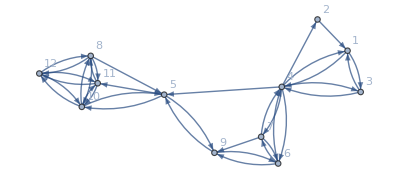

{{1,2,3,4},{5,6,7,9},{8,10,11,12}}

```mathematica
edgeListFullExample1={1->3,1->4,2->1,3->1,3->4,4->1,4->2,4->3,4->5,4->6,4->7,6->4,7->4,8->10,8->5,5->10,5->11,10->5,10->11,10->8,11->10,9->5,10->12,8->11,5->9,6->7,6->9,7->6,7->9,9->6,8->12,11->8,12->8,12->10,12->11,11->12};
graphExample1=Graph[edgeListFullExample1,VertexLabels->"Name"]
cmExample1=Normal[Transpose[AdjacencyMatrix[Graph[edgeListFullExample1]]]];
dynExample1={"OR","OR","AND","OR","AND","OR","OR","AND","AND","OR","OR","AND"};
csExample1=calculateOneOutptuOfNetwork[{0,0,0,0,0,0,0,0,0,0,0,0},cmExample1,dynExample1]["Output"];
subnetworksExample1={{1->3,1->4,2->1,3->1,3->4,4->1,4->2,4->3},{9->5,9->6,5->9,6->7,6->9,7->6,7->9},{8->10,8->11,8->12,10->11,10->8,10->12,11->8,11->12,11->10,12->8,12->10,12->11}};
vlsubnetworksExample1=Table[Sort[VertexList[Graph[subnetworksExample1[[gg]]]]],{gg,1,Length[subnetworksExample1],1}]
```

```mathematica
analysisBasinsAttractionTest[myInputs_,myOutputs_,currentState_,path_String:""]:=Module[{assoInputsOutputs,attAndItsInputs,qq,flatAtts,inputsPerAtt,assAttAndInputs,allPatterns,ff,gg,assPattOfInputsAndAtt,ll,assInputPattersToAtts,onlyPattOfAtts,onlyInputsPattToAtts,mm,changesInInputs,effectInOutputs,atts,whereCSIs,kk},

assoInputsOutputs=Table[Association[Part[myInputs,qq]->Part[myOutputs,qq]],{qq,1,Length[myInputs],1}];
attAndItsInputs=GroupBy[assoInputsOutputs,Values];

(*flat attractors*)
atts=Keys[attAndItsInputs];
flatAtts=Map[Flatten[#]&,Keys[attAndItsInputs]];

(*number of inputs per attractor*)inputsPerAtt=Table[Map[Flatten[#]&,Keys[attAndItsInputs[Part[atts,ff]]]],{ff,1,Length[atts],1}];
(*association attractors->Inputs*)assAttAndInputs=Table[Association[<|Part[flatAtts,gg]->Part[inputsPerAtt,gg]|>],{gg,1,Length[flatAtts],1}];
assAttAndInputs=SortBy[assAttAndInputs,Identity];

(*begin---------------------------*)
(*Print["Attractors and its inputs"];
Print[assAttAndInputs//TableForm];*)
(*end------------------------------*)


whereCSIs=Position[Keys[assAttAndInputs],currentState][[1]];
(*Print["Current state is in place:" <> ToString[whereCSIs]];*)

If[whereCSIs≠{1,1},assAttAndInputs=Permute[assAttAndInputs,Cycles[{{1,whereCSIs[[1]][[1]]}}]];
Print["CS moved to first place"];
Print[assAttAndInputs//TableForm];
,Null(*Print["No need to put cs as first element"]*)];


allPatterns=findPatternsInInputsPerAttTotal[Flatten[Values[assAttAndInputs],1]]["Pattern"];
flatAtts = Flatten[Keys[assAttAndInputs],1];
inputsPerAtt = Values[assAttAndInputs];

assPatt2Atts=Table[Association[<|Part[allPatterns,ll]->Flatten[Part[Keys[assAttAndInputs],ll],1]|>],{ll,1,Length[allPatterns],1}];


Print["Final Association"];
Print[assPatt2Atts//TableForm];


(*evaluate all intputs associated to attractors and find patternss*)(*allPatterns=findPatternsInInputsPerAttTotal[inputsPerAtt]["Pattern"];*)
(*associations between found patters in inputs and its attractors*)
(*

assPattOfInputsAndAtt=Table[Association[<|Part[allPatterns,ll]->Part[FlatAtts,ll]|>],{ll,1,Length[FlatAtts],1}];
(*associations sorted by number of "*"*)assInputPattersToAtts=KeySortBy[Merge[assPattOfInputsAndAtt,Identity],Count[#,"*"]&];
(*Only patterns in inputs*)onlyInputsPattToAtts=Keys[assInputPattersToAtts];
(*only attractors*)onlyPattOfAtts=Flatten[#]&/@Values[assInputPattersToAtts];
(*look for position in the list of attractors the current state*)(*whereCSIs=Position[onlyPattOfAtts,currentState][[1]];*)(*begin-------------------------------------*)(*Print["cs is in: "<>ToString[whereCSIs]<>" in:"];
Print[onlyPattOfAtts];
Print[onlyInputsPattToAtts];*)kk=Keys[assInputPattersToAtts];
whereCSIs=Position[Keys[assInputPattersToAtts],currentState][[1]];
Print["cs is in: "<>ToString[whereCSIs]<>" in:"];
Print[assInputPattersToAtts//TableForm];
(*end---------------------------------------*)(*and locate it in the beggining of list*)(*If[whereCSIs≠{1},onlyPattOfAtts=Permute[onlyPattOfAtts,Cycles[{{1,whereCSIs[[1]]}}]];
onlyInputsPattToAtts=Permute[onlyInputsPattToAtts,Cycles[{{1,whereCSIs[[1]]}}]],Null];*)
(*begin-------------------------*)(*Print["New arragement:"];
Print[onlyPattOfAtts];
Print[onlyInputsPattToAtts];*)(*end-----------------------------*)



changesInInputs=Table[giveIndexesOfDifferences[Part[onlyInputsPattToAtts,1],Part[onlyInputsPattToAtts,mm]]["Differences"],{mm,2,Length[onlyInputsPattToAtts],1}];
effectInOutputs=Table[giveIndexesOfDifferences[Part[onlyPattOfAtts,1],Part[onlyPattOfAtts,mm]]["Differences"],{mm,2,Length[onlyPattOfAtts],1}];

*)

changesInInputs=Table[giveIndexesOfDifferences[Part[allPatterns,1],Part[allPatterns,mm]]["Differences"],{mm,2,Length[allPatterns],1}];
effectInOutputs=Table[giveIndexesOfDifferences[Part[flatAtts,1],Part[flatAtts,mm]]["Differences"],{mm,2,Length[flatAtts],1}];

(*If a path is definted,results are saved*)
If[path≠"",Export[path<>"InputsPerAttractor.csv",inputsPerAtt,"CSV"];
Export[path<>"Attractors.csv",flatAtts,"CSV"];
Export[path<>"InputPatters2Attractors.csv",allPatterns,"CSV"];,Null];

<|
"ChangeInNodes"->changesInInputs,
"EffectInNodes"->effectInOutputs,
"ImputsPerAttractor"->inputsPerAtt,
"Attractors"->flatAtts,
"PatternsOfInputs"->allPatterns,
"AssociationInputs2Attractors"->assAttAndInputs
|>];
```

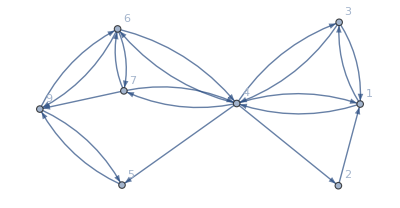

queis

NewVertex:{1, 2, 6, 7, 8}

NewVertex:{2, 4, 5, 6, 7}

```mathematica
edgeList2SubNets={1->3,1->4,2->1,3->1,3->4,4->1,4->2,4->3,4->5,4->6,4->7,6->4,7->4,9->5,5->9,6->7,6->9,7->6,7->9,9->6};

graph2SubNets=Graph[edgeList2SubNets,VertexLabels->"Name"]
cm2SubNets=ConstantArray[0,{Length[VertexList[graph2SubNets]],Length[VertexList[graph2SubNets]]}];

(*Create connectivity matrix from edge List*)
group=KeySort[GroupBy[edgeList2SubNets,First]];
whoReceives=#[[2]]&/@#&/@Values[group];
newNames = Range[1,Length[whoReceives]];
origNames =Sort[ Keys[group]];
Thread[newNames-> origNames];
whoReceives=whoReceives/.{Thread[origNames->newNames]}[[1]];

Print["queis"];
queis=Keys[group]/.{Thread[origNames->newNames]}[[1]];
cm2SubNets=Transpose[Table[ReplacePart[cm2SubNets[[queis[[qq]]]],Thread[whoReceives[[qq]]-> 1]],{qq,1,Length[whoReceives],1}]];


dyn2SubNets={"OR","OR","AND","OR","AND","OR","OR","AND"};
cs2SubNets=calculateOneOutptuOfNetwork[{0,0,0,0,0,0,0,0},cm2SubNets,dyn2SubNets]["Output"];

rd=runDynamicHD[cm2SubNets,dyn2SubNets,"/Users/macbookpro/Documents/","normal"];

aba=analysisBasinsAttractionTest[rd["RepertoireInputs"],rd["RepertoireOutputs"],cs2SubNets,"/Users/macbookpro/Documents/"];


pdcs=probabDistribCalcSubnetwork[{1,2,3,4,5,6,7,9},{1,2,6,7,9},{2,4,5,6,7},rd["RepertoireOutputs"],rd["RepertoireInputs"],cs2SubNets,"causal"];
```

```mathematica
(* Only this 2 inputs leads to "0,0,0,0,0,0,0,0" attractor*)
(*calculateOneOutptuOfNetwork[{0,0,0,0,0,0,0,0},cm2SubNets,dyn2SubNets]["Output"]
calculateOneOutptuOfNetwork[{0,0,0,0,1,0,0,0},cm2SubNets,dyn2SubNets]["Output"]*)


calculateOneOutptuOfNetwork[{1,0,0,0,0,0,0,0},cm2SubNets,dyn2SubNets]["Output"]
calculateOneOutptuOfNetwork[{1,0,0,0,1,0,0,0},cm2SubNets,dyn2SubNets]["Output"]
calculateOneOutptuOfNetwork[{1,0,0,0,0,1,0,0},cm2SubNets,dyn2SubNets]["Output"]
calculateOneOutptuOfNetwork[{1,0,0,0,1,1,0,0},cm2SubNets,dyn2SubNets]["Output"]
calculateOneOutptuOfNetwork[{1,0,0,0,0,0,1,0},cm2SubNets,dyn2SubNets]["Output"]
calculateOneOutptuOfNetwork[{1,0,0,0,1,0,1,0},cm2SubNets,dyn2SubNets]["Output"]
calculateOneOutptuOfNetwork[{1,0,0,0,0,1,1,0},cm2SubNets,dyn2SubNets]["Output"]
calculateOneOutptuOfNetwork[{1,0,0,0,1,1,1,0},cm2SubNets,dyn2SubNets]["Output"]
calculateOneOutptuOfNetwork[{1,0,0,0,0,0,0,1},cm2SubNets,dyn2SubNets]["Output"]
calculateOneOutptuOfNetwork[{1,0,0,0,1,0,0,1},cm2SubNets,dyn2SubNets]["Output"]
calculateOneOutptuOfNetwork[{1,0,0,0,0,1,0,1},cm2SubNets,dyn2SubNets]["Output"]
calculateOneOutptuOfNetwork[{1,0,0,0,1,1,0,1},cm2SubNets,dyn2SubNets]["Output"]
calculateOneOutptuOfNetwork[{1,0,0,0,0,0,1,1},cm2SubNets,dyn2SubNets]["Output"]
calculateOneOutptuOfNetwork[{1,0,0,0,1,0,1,1},cm2SubNets,dyn2SubNets]["Output"]
calculateOneOutptuOfNetwork[{1,0,0,0,0,1,1,1},cm2SubNets,dyn2SubNets]["Output"]
calculateOneOutptuOfNetwork[{1,0,0,0,1,1,1,1},cm2SubNets,dyn2SubNets]["Output"]
```

{0,0,0,1,0,0,0,0}

{0,0,0,1,0,0,0,0}

{0,0,0,1,0,0,1,0}

{0,0,0,1,0,0,1,0}

{0,0,0,1,0,1,0,0}

{0,0,0,1,0,1,0,0}

{0,0,0,1,0,1,1,0}

{0,0,0,1,0,1,1,1}

{0,0,0,1,0,1,0,0}

{0,0,0,1,0,1,0,0}

{0,0,0,1,0,1,1,0}

{0,0,0,1,0,1,1,0}

{0,0,0,1,0,1,0,0}

{0,0,0,1,0,1,0,0}

{0,0,0,1,0,1,1,0}

{0,0,0,1,0,1,1,1}

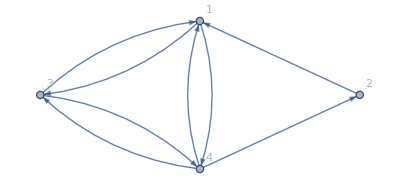

{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}

<|1→{1→3,1→4},2→{2→1},3→{3→1,3→4},4→{4→1,4→2,4→3}|>

{{3,4},{1},{1,4},{1,2,3}}

{1,2,3,4}

{1,2,3,4}

{1→1,2→2,3→3,4→4}

{{3,4},{1},{1,4},{1,2,3}}

queis

{1,2,3,4}

{{0,1,1,1},{0,0,0,1},{1,0,0,1},{1,0,1,0}}

{0,0,0,0}

Final Association

<|{0,0,0,0}→{0,0,0,0}|>
<|{1,0,0,0}→{0,0,0,1}|>
<|{0,1,0,0}→{1,0,0,0}|>
<|{*,*,*,0}→{1,0,0,1}|>
<|{0,*,0,1}→{1,1,0,0}|>
<|{0,*,1,1}→{1,1,0,1}|>
<|{1,*,*,1}→{1,1,1,1}|>

<|ChangeInNodes→{{1},{2},{1,2,3},{2,4},{2,3,4},{1,2,3,4}},EffectInNodes→{{4},{1},{1,4},{1,2},{1,2,4},{1,2,3,4}},ImputsPerAttractor→{{{{0,0,0,0}}},{{{1,0,0,0}}},{{{0,1,0,0}}},{{{1,1,0,0},{0,0,1,0},{1,0,1,0},{0,1,1,0},{1,1,1,0}}},{{{0,0,0,1},{0,1,0,1}}},{{{0,0,1,1},{0,1,1,1}}},{{{1,0,0,1},{1,1,0,1},{1,0,1,1},{1,1,1,1}}}},Attractors→{{0,0,0,0},{0,0,0,1},{1,0,0,0},{1,0,0,1},{1,1,0,0},{1,1,0,1},{1,1,1,1}},PatternsOfInputs→{{0,0,0,0},{1,0,0,0},{0,1,0,0},{*,*,*,0},{0,*,0,1},{0,*,1,1},{1,*,*,1}},AssociationInputs2Attractors→{<|{0,0,0,0}→{{0,0,0,0}}|>,<|{0,0,0,1}→{{1,0,0,0}}|>,<|{1,0,0,0}→{{0,1,0,0}}|>,<|{1,0,0,1}→{{1,1,0,0},{0,0,1,0},{1,0,1,0},{0,1,1,0},{1,1,1,0}}|>,<|{1,1,0,0}→{{0,0,0,1},{0,1,0,1}}|>,<|{1,1,0,1}→{{0,0,1,1},{0,1,1,1}}|>,<|{1,1,1,1}→{{1,0,0,1},{1,1,0,1},{1,0,1,1},{1,1,1,1}}|>}|>

NewVertex:{1, 2}

NewVertex:{2, 4}

<|OutputsWithCurrentSubstate→{{0,0,0,0},{0,0,0,1}},IndexesOutElementsCurrentSubstate→{1,2},PossiblePastFutureStates→{{0,0,0,0},{1,0,0,0}},PurviewsOfPossiblePastFutureStates→{{0,0},{0,0}},SingleProbability→0.5,AllPatternsPurviews→<|{0,0}→2|>,CompleteProbabilityDistribution→{1.,1.,0,0,1.,1.,0,0,0,0,0,0,0,0,0,0}|>

```mathematica
edgeListM1={1->3,1->4,2->1,3->1,3->4,4->1,4->2,4->3};

graphM1=Graph[edgeListM1,VertexLabels->"Name"]
cmM1=ConstantArray[0,{Length[VertexList[graphM1]],Length[VertexList[graphM1]]}]

(*Create connectivity matrix from edge List*)
groupM1=KeySort[GroupBy[edgeListM1,First]]
whoReceiveM1=#[[2]]&/@#&/@Values[groupM1]
newNamesM1 = Range[1,Length[whoReceiveM1]]
origNamesM1 =Sort[ Keys[groupM1]]
Thread[newNamesM1-> origNamesM1]
whoReceiveM1=whoReceiveM1/.{Thread[origNamesM1->newNamesM1]}[[1]]

Print["queis"]
queisM1=Keys[groupM1]/.{Thread[origNamesM1->newNamesM1]}[[1]]
cmM1=Transpose[Table[ReplacePart[cmM1[[queisM1[[qq]]]],Thread[whoReceiveM1[[qq]]-> 1]],{qq,1,Length[whoReceiveM1],1}]]




dynM1={"OR","OR","AND","OR"};
csM1=calculateOneOutptuOfNetwork[{0,0,0,0},cmM1,dynM1]["Output"]

rdM1=runDynamicHD[cmM1,dynM1,"/Users/macbookpro/Documents/M1/","inverse"];

abaM1=analysisBasinsAttractionTest[rdM1["RepertoireInputs"],rdM1["RepertoireOutputs"],csM1,"/Users/macbookpro/Documents/M1/"]

pdcsM1=probabDistribCalcSubnetwork[{1,2,3,4},{1,2},{2,4},rdM1["RepertoireOutputs"],rdM1["RepertoireInputs"],csM1,"causal"]
```

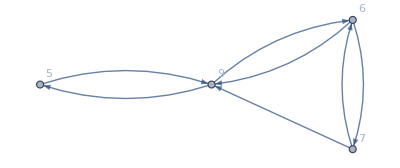

{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}

<|5→{5→9},6→{6→7,6→9},7→{7→6,7→9},9→{9→5,9→6}|>

{{9},{7,9},{6,9},{5,6}}

{1,2,3,4}

{5,6,7,9}

{1→5,2→6,3→7,4→9}

{{4},{3,4},{2,4},{1,2}}

queis

{5,6,7,9}

{1,2,3,4}

{{0,0,0,1},{0,0,1,1},{0,1,0,0},{1,1,1,0}}

{0,0,0,0}

Final Association

<|{*,0,0,0}→{0,0,0,0}|>
<|{*,1,0,0}→{0,0,1,0}|>
<|{*,0,1,0}→{0,1,0,0}|>
<|{0,1,1,0}→{0,1,1,0}|>
<|{1,1,1,0}→{0,1,1,1}|>
<|{*,0,*,1}→{1,1,0,0}|>
<|{*,1,*,1}→{1,1,1,0}|>
<|{1,1,1,1}→{1,1,1,1}|>

<|ChangeInNodes→{{2},{3},{1,2,3},{1,2,3},{3,4},{2,3,4},{1,2,3,4}},EffectInNodes→{{3},{2},{2,3},{2,3,4},{1,2},{1,2,3},{1,2,3,4}},ImputsPerAttractor→{{{{0,0,0,0},{1,0,0,0}}},{{{0,1,0,0},{1,1,0,0}}},{{{0,0,1,0},{1,0,1,0}}},{{{0,1,1,0}}},{{{1,1,1,0}}},{{{0,0,0,1},{1,0,0,1},{0,0,1,1},{1,0,1,1}}},{{{0,1,0,1},{1,1,0,1},{0,1,1,1}}},{{{1,1,1,1}}}},Attractors→{{0,0,0,0},{0,0,1,0},{0,1,0,0},{0,1,1,0},{0,1,1,1},{1,1,0,0},{1,1,1,0},{1,1,1,1}},PatternsOfInputs→{{*,0,0,0},{*,1,0,0},{*,0,1,0},{0,1,1,0},{1,1,1,0},{*,0,*,1},{*,1,*,1},{1,1,1,1}},AssociationInputs2Attractors→{<|{0,0,0,0}→{{0,0,0,0},{1,0,0,0}}|>,<|{0,0,1,0}→{{0,1,0,0},{1,1,0,0}}|>,<|{0,1,0,0}→{{0,0,1,0},{1,0,1,0}}|>,<|{0,1,1,0}→{{0,1,1,0}}|>,<|{0,1,1,1}→{{1,1,1,0}}|>,<|{1,1,0,0}→{{0,0,0,1},{1,0,0,1},{0,0,1,1},{1,0,1,1}}|>,<|{1,1,1,0}→{{0,1,0,1},{1,1,0,1},{0,1,1,1}}|>,<|{1,1,1,1}→{{1,1,1,1}}|>}|>

NewVertex:{2, 3, 4}

NewVertex:{1, 2, 3}

<|OutputsWithCurrentSubstate→{{0,0,0,0},{0,0,0,0}},IndexesOutElementsCurrentSubstate→{1,2},PossiblePastFutureStates→{{0,0,0,0},{1,0,0,0}},PurviewsOfPossiblePastFutureStates→{{0,0,0},{1,0,0}},SingleProbability→0.5,AllPatternsPurviews→<|{0,0,0}→1,{1,0,0}→1|>,CompleteProbabilityDistribution→{0.5,0.5,0,0,0,0,0,0,0.5,0.5,0,0,0,0,0,0}|>

```mathematica
edgeListM2={9->5,9->6,5->9,6->7,6->9,7->6,7->9};


graphM2=Graph[edgeListM2,VertexLabels->"Name"]
cmM2=ConstantArray[0,{Length[VertexList[graphM2]],Length[VertexList[graphM2]]}]

(*Create connectivity matrix from edge List*)
groupM2=KeySort[GroupBy[edgeListM2,First]]
whoReceiveM2=#[[2]]&/@#&/@Values[groupM2]
newNamesM2 = Range[1,Length[whoReceiveM2]]
origNamesM2 =Sort[ Keys[groupM2]]
Thread[newNamesM2-> origNamesM2]
whoReceiveM2=whoReceiveM2/.{Thread[origNamesM2->newNamesM2]}[[1]]

Print["queis"]
Keys[groupM2]
queisM2=Keys[groupM2]/.{Thread[origNamesM2->newNamesM2]}[[1]]

(*cmM2=Table[ReplacePart[cmM2[[queisM2[[qq]]]],Thread[whoReceiveM2[[qq]]-> 1]],{qq,1,Length[whoReceiveM2],1}]*)

cmM2=Transpose[Table[ReplacePart[cmM2[[queisM2[[qq]]]],Thread[whoReceiveM2[[qq]]-> 1]],{qq,1,Length[whoReceiveM2],1}]]




dynM2={"AND","OR","OR","AND"};
csM2=calculateOneOutptuOfNetwork[{0,0,0,0},cmM2,dynM2]["Output"]

rdM2=runDynamicHD[cmM2,dynM2,"/Users/macbookpro/Documents/M2/","inverse";
analysisBasinsAttractionTest [rdM2["RepertoireInputs"],rdM2["RepertoireOutputs"],csM2,"/Users/macbookpro/Documents/M2/"]

pdcsM2=probabDistribCalcSubnetwork[{5,6,7,9},{6,7,9},{5,6,7},rdM2["RepertoireOutputs"],rdM2["RepertoireInputs"],csM2,"causal"]
```

```mathematica
calculateOneOutptuOfNetwork[{0,0,0,0},cmM2,dynM2]["Output"]
calculateOneOutptuOfNetwork[{1,0,0,0},cmM2,dynM2]["Output"]
```

{0,0,0,0}

{0,0,0,0}

```mathematica
probM1= pdcsM1["CompleteProbabilityDistribution"]
probM2= pdcsM2["CompleteProbabilityDistribution"]
ConstantArray[1/16,16]
comDist=Flatten[probM1*#&/@ probM2]
Position[comDist,0.5]
```

{1.,1.,0,0,1.,1.,0,0,0,0,0,0,0,0,0,0}

{0.5,0.5,0,0,0,0,0,0,0.5,0.5,0,0,0,0,0,0}

{1/16,1/16,1/16,1/16,1/16,1/16,1/16,1/16,1/16,1/16,1/16,1/16,1/16,1/16,1/16,1/16}

{0.5,0.5,0.,0.,0.5,0.5,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.5,0.5,0.,0.,0.5,0.5,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0,0,0.,0.,0,0,0,0,0,0,0,0,0,0,0.,0.,0,0,0.,0.,0,0,0,0,0,0,0,0,0,0,0.,0.,0,0,0.,0.,0,0,0,0,0,0,0,0,0,0,0.,0.,0,0,0.,0.,0,0,0,0,0,0,0,0,0,0,0.,0.,0,0,0.,0.,0,0,0,0,0,0,0,0,0,0,0.,0.,0,0,0.,0.,0,0,0,0,0,0,0,0,0,0,0.5,0.5,0.,0.,0.5,0.5,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.5,0.5,0.,0.,0.5,0.5,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0,0,0.,0.,0,0,0,0,0,0,0,0,0,0,0.,0.,0,0,0.,0.,0,0,0,0,0,0,0,0,0,0,0.,0.,0,0,0.,0.,0,0,0,0,0,0,0,0,0,0,0.,0.,0,0,0.,0.,0,0,0,0,0,0,0,0,0,0,0.,0.,0,0,0.,0.,0,0,0,0,0,0,0,0,0,0,0.,0.,0,0,0.,0.,0,0,0,0,0,0,0,0,0,0}

{{1},{2},{5},{6},{17},{18},{21},{22},{129},{130},{133},{134},{145},{146},{149},{150}}

```mathematica
{{1},{2},{5},{6},{17},{18},{21},{22},{129},{130},{133},{134},{145},{146},{149},{150}}
{{1},{2},{5},{6},{17},{18},{21},{22},{129},{130},{133},{134},{145},{146},{149},{150}}
```

```mathematica
2^110
```

1298074214633706907132624082305024

```mathematica
dm1=EuclideanDistance[ConstantArray[1/16,16],probM1]
dm2=EuclideanDistance[ConstantArray[1/16,16],probM2]
EuclideanDistance[ConstantArray[1/256,256],comDist]
dm1*dm2
```

1.88746

0.901388

1.9853

1.70133

```mathematica
EuclideanDistance[{0.5,0.5},{dm2,dm1}]
```

1.44435

```mathematica
Solve[Sqrt[((dm1-x)^2) +((dm2-x)^2)]==1.9853,x]
```

{{x→0.080032},{x→2.70881}}

```mathematica
edgeList2BNSFormat[edgeList_, dynamic_, direction_]:= Module[
{},
cm = edgelist2CM[edgeList]["CM"];
bigString = "";
nodeList = "";

For[jj=1, jj≤ Length[cm],jj++,
howManyInputs = Count[cm[[jj]],1];
whoInput =StringReplace[ToString[Flatten[Position[cm[[jj]],1]]],","->  ""];
fistLine = StringReplace[StringReplace[".n " <> ToString[jj] <> " " <> ToString[howManyInputs] <> " " <>whoInput,"{"-> ""],"}"-> ""];

nodeList=nodeList<> ToString[jj]<> "\n";

If[direction=== "inverse",allPosibleInputsReverse[howManyInputs], 
inputs = allPosibleInputsNormal[howManyInputs]];

outputs = Table[executeBooleanRule[inputs[[ww]],dynamic[[jj]]],{ww,1,Length[inputs],1}];

line = "";


For[hh=1, hh≤ Length[inputs],hh++,

line = StringReplace[StringReplace[line <>StringReplace[ToString[inputs[[hh]]],", "-> ""]<> " " <> ToString[outputs[[hh]]],"{"-> ""],"}"-> ""] <> "\n";

];

bigString= bigString <> fistLine<> "\n" <> line <> "\n";
];



<|
"BNSFormatStr" ->  bigString,
"NodeListStr"-> nodeList
|>
];
```

```mathematica
edgeList2SubNets={1->3,1->4,2->1,3->1,3->4,4->1,4->2,4->3,4->5,4->6,4->7,6->4,7->4,9->5,5->9,6->7,6->9,7->6,7->9,9->6};
dyn2SubNets={"OR","OR","AND","OR","AND","OR","OR","AND"};


bnsFormat = edgeList2BNSFormat[edgeList2SubNets,dyn2SubNets,"normal"];
Export["/Users/macbookpro/Documents/03_REDUCTION_NETWORKS/PAD/BNSFile.txt",bnsFormat["BNSFormatStr"]];
Export["/Users/macbookpro/Documents/03_REDUCTION_NETWORKS/PAD/NodeList.txt",bnsFormat["NodeListStr"]];

(*graph2SubNets=Graph[edgeList2SubNets,VertexLabels->"Name"];
network2BNSFormat[graph2SubNets]*)
```

```mathematica
edgeListM1={1->3,1->4,2->1,3->1,3->4,4->1,4->2,4->3};
dynM1={"OR","OR","AND","OR"};

bnsFormat1 = edgeList2BNSFormat[edgeListM1,dynM1,"normal"];
Export["/Users/macbookpro/Documents/03_REDUCTION_NETWORKS/PAD/BNS4nFile.txt",bnsFormat1["BNSFormatStr"]];
Export["/Users/macbookpro/Documents/03_REDUCTION_NETWORKS/PAD/Node4nList.txt",bnsFormat1["NodeListStr"]];
```